## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]

(* Declare external momenta. *)
DeclareLorentzVectors[q,k1,p1,p2,k2,l];

(* Declare real parameters + kinematics *)
DeclareReal[gs,e,eH,eL, m2,q2];
DeclareReal[s,sp,s3,s4,s5,t,tp,tpsp,t1,u,up,u1,u5,u6,u7];

norm={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u->u1+m2,u1p->u1-q2};
massSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[k2]-> 0};
(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

(* debug tools *)
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

```mathematica
DeclareRealHEPTensor[{gluonTensor,projG,projL[_]},{Lorentz,Lorentz}];
DeclareHEPTensor[{projP[_,_],polGluonTensor[_,_]},{Lorentz,Lorentz}];
gluonTensor[μ_,ν_]=-Eta[μ,ν];
projG[μ_,ν_]=-Eta[μ,ν];
projL[k_][μ_,ν_]:=-4q2/sp^2 k[μ]k[ν];
projP[q1_,p_][μ_,ν_]:=I HEPMultiply[Eps[μ,ν,ρ,σ] q1[ρ] p[σ]]/SDot[q1,p]
polGluonTensor[q_,p_][μ_,ν_]:=projP[q,p][μ,ν];

getGetNLOMe[kinVars_]:=me↦Module[{mxe},
mxe=CalcDiracTraces@me;
mxe=LorentzContract@HEPExpand@mxe;
mxe=RemoveEpsDot@mxe;
(* replace HDots *)
mxe=mxe/.{HDot[k2,k2]-> -k2hat2,HDot[p1,p1]-> -k2hat2,HDot[k2,p1]-> k2hat2,HDot[a_,b_]:> 0};
(* insert masses *)
mxe=Expand[mxe/.massSub];
(* insert all kinematic variables *)
mxe=Expand[mxe/.momentumVectorSDots];
(* remove some kinematic variables *)
mxe=Expand[mxe//.kinVars];
mxe=Expand[mxe/8/.{Dim-> 4+ϵ}/.norm];
mxe
]
```

```mathematica
(* remove EpsDot in favour of SDot and HDot; based on TRACER and Wikipedia *)
Module[{f,a1,a2,a3,a4,b1,b2,b3,b4,cache,replace,rest},
(* master formula *)
f[ps_,qs_]:=Module[{l,mus,mups,d},
l=Length[ps];
mus=Table[Unique[],{l}];
mups=Table[Unique[],{l}];
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply@@Join[{d},(e↦(e[[1]])[(e[[2]])])/@Transpose[{ps,mus}],(e↦(e[[1]])[(e[[2]])])/@Transpose[{qs,mups}]]
];
(* cache elements *)
cache={
EpsDot[p1_][mu_,nu_,rho_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1},{a1}]/.{a1->p1}],
EpsDot[p1_][mu_,nu_,rho_]EpsDot[k1_][mu_,nu_,rho_]:>Evaluate[LorentzContract@HEPExpand@f[{a1},{b1}]/.{a1->p1,b1->k1}],
EpsDot[p1_,p2_][mu_,nu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{a1,a2}]/.{a1->p1,a2->p2}],
EpsDot[p1_,p2_][mu_,nu_]EpsDot[k1_,k2_][mu_,nu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{b1,b2}]/.{a1->p1,a2->p2,b1->k1,b2->k2}],
EpsDot[p1_,p2_,p3_][mu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{a1,a2,a3}]/.{a1->p1,a2->p2,a3->p3}],
EpsDot[p1_,p2_,p3_][mu_]EpsDot[k1_,k2_,k3_][mu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{b1,b2,b3}]/.{a1->p1,a2->p2,a3->p3,b1->k1,b2->k2,b3->k3}],
EpsDot[p1_,p2_,p3_,p4_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{a1,a2,a3,a4}]/.{a1->p1,a2->p2,a3->p3,a4->p4}],
EpsDot[p1_,p2_,p3_,p4_]EpsDot[k1_,k2_,k3_,k4_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{b1,b2,b3,b4}]/.{a1->p1,a2->p2,a3->p3,a4->p4,b1->k1,b2->k2,b3->k3,b4->k4}]
};
(* handle uncontracted; suppressed atm *)
rest={
Eps[nus__]Eps[nups__]:> Module[{l,mus,mups,d},
l=4;
mus={nus};
mups={nups};
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply[d]
]
};
(* replace all *)
replace[e_]:=e/.{
Sqr[EpsDot[p1_,p2_,p3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]^2],
SDot[EpsDot[p1_,p2_,p3_],EpsDot[k1_,k2_,k3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]EpsDot[k1,k2,k3][mu]]
}/.cache(*/.rest*);
(* function to call *)
RemoveEpsDot[ex_]:=Module[{e},
e=ex;
If[FreeQ[e,EpsDot]&&FreeQ[e,Eps],Return[e]];
e=SortEps@e;
If[Head[e]===Plus,e=Parallelize[Sum[replace[e[[k]]],{k,Length@e}]],e=replace[e]];
LorentzContract@HEPExpand@e
];
]
```

## LO γ*(q)+g(k1) → Q(p1)+Qbar(p2)

### Matrix elements

```mathematica
meLOt1[μ_,ν_]:=Ga[μ].(Gs[k1-p2]+Sqrt[m2] GI).Ga[ν]/t1;
meLOt1CC[μ_,ν_]:=Ga[ν].(Gs[k1-p2]+Sqrt[m2] GI).Ga[μ]/t1;
meLOu1[μ_,ν_]:=Ga[ν].(Gs[p1-k1]+Sqrt[m2] GI).Ga[μ]/u1;
meLOu1CC[μ_,ν_]:=Ga[μ].(Gs[p1-k1]+Sqrt[m2] GI).Ga[ν]/u1;
meLO[μ1_,ν1_]:=meLOt1[μ1,ν1]+meLOu1[μ1,ν1];
meLOCC[μ1_,ν1_]:=meLOt1CC[μ1,ν1]+meLOu1CC[μ1,ν1];

BornVectorSDots={
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2,
HDot[a_,b_]:> 0
};
```

```mathematica
getBQED[ex_]:=Module[{e},
e=ex;
e=LorentzContract@HEPExpand@CalcDiracTraces@e;
e=RemoveEpsDot@SortEps@e;
e=Simplify[e/(8)/.{Dim-> 4+ϵ}/.norm/.Join[massSub,BornVectorSDots]];
e
]
BGQED=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projG[μ,μp],gluonTensor[ν,νp]]]
BLQED=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projL[k1][μ,μp],gluonTensor[ν,νp]]]
BPQED=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projP[q,k1][μ,μp],polGluonTensor[k1,q][ν,νp]]]
```

(-16 m2^2 (t1+u1)^2+t1 u1 (2+ϵ) (4 q2^2+4 sp^2+2 t1^2+2 u1^2+4 sp (t1+u1)+4 q2 (2 sp+t1+u1)+t1^2 ϵ+2 t1 u1 ϵ+u1^2 ϵ)-4 m2 ((t1+u1)^3 (2+ϵ)+q2 (2 t1 u1 ϵ+t1^2 (2+ϵ)+u1^2 (2+ϵ))+sp (2 t1 u1 ϵ+t1^2 (2+ϵ)+u1^2 (2+ϵ))))/(4 t1^2 u1^2)

-(4 q2 ((q2+sp) t1 u1-m2 (t1+u1)^2))/(sp^2 t1 u1)

(-2 m2 sp (t1^3+t1^2 u1+t1 u1^2+u1^3)+t1 u1 (sp^2 (t1+u1)+(t1-u1)^2 (t1+u1)+sp (t1^2+u1^2)+q2 (-(t1-u1)^2+sp (t1+u1))))/(sp t1^2 u1^2)

### Check to Nucl.Phys.B 392-162

```mathematica
Collect[Expand[BGQED/.{sp-> -t1-u1}],{ϵ}]
BGQEDref = t1/u1 + u1/t1 + 4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2 sp q2/(t1 u1) + 2q2^2/(t1 u1) +2m2 q2/(t1 u1)(2- sp^2/(t1 u1))+ϵ(-1+(sp^2+sp q2 + q2^2)/(t1 u1) - m2 q2 sp^2/(t1^2 u1^2)) + ϵ^2sp^2/(4t1 u1);
Collect[Expand[BGQEDref/.{sp-> -t1-u1}],{ϵ}]
Collect[FullSimplify[(BGQED/.{sp-> -t1-u1,Dim-> 4+ϵ})-(BGQEDref/.{sp-> -t1-u1})],ϵ]
```

-(4 m2^2)/t1^2-(2 m2 q2)/t1^2-(4 m2)/t1-(2 q2)/t1-(4 m2^2)/u1^2-(2 m2 q2)/u1^2-(4 m2)/u1-(2 q2)/u1-(8 m2^2)/(t1 u1)+(2 q2^2)/(t1 u1)+t1/u1+u1/t1+(1-(m2 q2)/t1^2-q2/t1-(m2 q2)/u1^2-q2/u1-(2 m2 q2)/(t1 u1)+q2^2/(t1 u1)+t1/u1+u1/t1) ϵ+(1/2+t1/(4 u1)+u1/(4 t1)) ϵ^2

-(4 m2^2)/t1^2-(2 m2 q2)/t1^2-(4 m2)/t1-(2 q2)/t1-(4 m2^2)/u1^2-(2 m2 q2)/u1^2-(4 m2)/u1-(2 q2)/u1-(8 m2^2)/(t1 u1)+(2 q2^2)/(t1 u1)+t1/u1+u1/t1+(1-(m2 q2)/t1^2-q2/t1-(m2 q2)/u1^2-q2/u1-(2 m2 q2)/(t1 u1)+q2^2/(t1 u1)+t1/u1+u1/t1) ϵ+(1/2+t1/(4 u1)+u1/(4 t1)) ϵ^2

0

```mathematica
Collect[Expand[BLQED/.{sp-> -t1-u1,Dim-> 4+ϵ}],{ϵ}]
BLQEDref = -4q2/sp((sp+q2)/sp-m2 sp/(t1 u1));
Collect[Expand[BLQEDref/.{sp-> -t1-u1}],{ϵ}]
Collect[FullSimplify[(BLQED/.{sp-> -t1-u1,Dim-> 4+ϵ})-(BLQEDref/.{sp-> -t1-u1})],ϵ]
```

(8 m2 q2)/(-t1-u1)^2-(4 q2^2)/(-t1-u1)^2+(4 q2 t1)/(-t1-u1)^2+(4 m2 q2 t1)/((-t1-u1)^2 u1)+(4 q2 u1)/(-t1-u1)^2+(4 m2 q2 u1)/(t1 (-t1-u1)^2)

-(4 q2^2)/(-t1-u1)^2+(4 q2 t1)/(-t1-u1)^2-(4 m2 q2)/(t1 (-t1-u1))-(4 m2 q2)/((-t1-u1) u1)+(4 q2 u1)/(-t1-u1)^2

0

### check to Marco

```mathematica
Marco`BPQED = << "~/Physik/PhD/Marco/recalc/data/BPQED"
Simplify[((Marco`BPQED/.{m^2-> m2})-BPQED)/.norm]
```

q2/sp-(2 m^2)/t1+s/t1-t1/sp-(2 m^2 t1)/u1^2-(2 m^2)/u1+s/u1+t1/u1-(q2 t1)/(sp u1)+t1^2/(sp u1)-(2 m^2 u1)/t1^2+u1/t1-u1p/sp+(u1 u1p)/(sp t1)

0

### old/HEP way

```mathematica
DeclareLorentzVectors[mxBornt1,mxBornu1,mxBorn];
mxBornt1[μ_]=(Bar[USp[p1][r1]].(-I eH e Ga[μ]).(I(Gs[k1-p2]+Sqrt[m2] GI)).(I gs Ga[ν]).VSp[p2][r2])/(t1)Pol[k1][λg,ν]*ColorT[a,j1,j2];
mxBornu1[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν]).(I(Gs[p1-k1]+Sqrt[m2] GI)).(-I eH e Ga[μ]).VSp[p2][r2])/(u1)Pol[k1][λg,ν]*ColorT[a,j1,j2];
mxBorn[μ_]=mxBornt1[μ]+mxBornu1[μ]
```

1/t1 ColorT[a,j1,j2] Bar[USp[p1]][r1].(-ⅈ e eH Ga[μ]).(ⅈ (GI √m2+Gs[k1-p2])).(ⅈ gs Ga[ν]).VSp[p2][r2] Pol[k1][λg,ν]+1/u1 ColorT[a,j1,j2] Bar[USp[p1]][r1].(ⅈ gs Ga[ν]).(ⅈ (GI √m2+Gs[-k1+p1])).(-ⅈ e eH Ga[μ]).VSp[p2][r2] Pol[k1][λg,ν]

```mathematica
Module[{ng,σG1,σG2,σG3,σG4,σG5,BGQED2},
(* guage vector *)
DeclareLorentzVectors[ng];
σG1=-HEPMultiply[mxBorn[mu],CC@mxBorn[mu]];
(* sum QQbar *)
σG2 = FermionPolarizationSums[σG1, {p1->Sqrt[m2], p2->Sqrt[m2]}];
(* sum g *)
σG3 = VectorPolarizationSums[σG2, {k1->ng}];
σG4 = σG3 // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce;(* eliminate Color *)
σG5=Simplify[σG4/.{Dim-> 4+ϵ}/.Join[massSub,{
Sqr[ng]->0, 
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}]];
BGQED2=σG5/(8gs^2 e^2 eH^2 (3 *4/3));
Simplify[BGQED-BGQED2]
]
```

0

```mathematica
Module[{ng,σL1,σL2,σL3,σL4,σL5,BLQED2},
(* guage vector *)
DeclareLorentzVectors[ng];
σL1=-4q2/sp^2 HEPMultiply[k1[mu], mxBorn[mu]]HEPMultiply[k1[nu],CC@mxBorn[nu]];
(* sum QQbar *)
σL2 = FermionPolarizationSums[σL1, {p1->Sqrt[m2], p2->Sqrt[m2]}];
(* sum g *)
σL3 = VectorPolarizationSums[σL2, {k1->ng}];
σL4 = σL3 // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce;(* eliminate Color *);
σL5=Simplify[σL4/.Join[massSub,{
Sqr[ng]->0, 
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}]];
BLQED2=σL5/(8gs^2 e^2 eH^2 (3 *4/3));
Simplify[BLQED-BLQED2]
]
```

0

## NLO γ*(q)+q(k1) → Q(p1)+Qbar(p2)+q(k2)

### 2 → 3 phasespace

```mathematica
momentumVectorSDots={
SDot[q,k1]->(s-q2)/2,
SDot[k2,p2]->s3/2,
SDot[k2,p1]->s4/2,
SDot[p1,p2]->(s5-2m2)/2,
SDot[k1,p2]->-t1/2,
SDot[k1,k2]->-tp/2,
SDot[q,p2]->-(u1-q2)/2,
SDot[k1,p1]->-u6/2,
SDot[q,p1]->-(u7-q2)/2,
SDot[q,k2]->-(up-q2)/2
};
kinematicConstraints = {
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
};
```

### Matrix elements

```mathematica
DeclareRealHEPTensor[{
meNLOγqalQ,meNLOγqalQCC,meNLOγqblQ,meNLOγqblQCC,meNLOγqablQ,meNLOγqablQCC,
meNLOγqclq,meNLOγqclqCC,meNLOγqdlq,meNLOγqdlqCC,meNLOγqcdlq,meNLOγqcdlqCC
},{Lorentz,Lorentz,Dirac,Dirac}];
DeclareRealHEPTensor[{meNLOγqabg,meNLOγqcdg},{Lorentz,Lorentz}];
meNLOγqalQ[μ_,νQ_]=(Ga[μ]).((Gs[p1-q]+Sqrt[m2] GI)/u7).(Ga[νQ]);
meNLOγqblQ[μ_,νQ_]=(Ga[νQ]).((Gs[q-p2]+Sqrt[m2] GI)/u1).(Ga[μ]);
meNLOγqalQCC[μ_,νQ_]=Reverse@meNLOγqalQ[μ,νQ];
meNLOγqblQCC[μ_,νQ_]=Reverse@meNLOγqblQ[μ,νQ];;
meNLOγqabg[νQ_,νq_]=gluonTensor[νQ,νq]/tp;
meNLOγqablQ[μ_,νQ_]=meNLOγqalQ[μ,νQ]+meNLOγqblQ[μ,νQ];
meNLOγqablQCC[μ_,νQ_]=meNLOγqalQCC[μ,νQ]+meNLOγqblQCC[μ,νQ];

meNLOγqclq[μ_,νq_]=(Ga[μ]).(Gs[k2-q]/up).(Ga[νq]);
meNLOγqdlq[μ_,νq_]=(Ga[νq]).(Gs[k1+q]/s).(Ga[μ]);
meNLOγqclqCC[μ_,νq_]=Reverse@meNLOγqclq[μ,νq];
meNLOγqdlqCC[μ_,νq_]=Reverse@meNLOγqdlq[μ,νq];
meNLOγqcdg[νQ_,νq_]=gluonTensor[νQ,νq]/s5;
meNLOγqcdlq[μ_,νq_]=meNLOγqclq[μ,νq]+meNLOγqdlq[μ,νq];
meNLOγqcdlqCC[μ_,νq_]=meNLOγqclqCC[μ,νq]+meNLOγqdlqCC[μ,νq];
```

### AGLi

```mathematica
getA1=getGetNLOMe[{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
getA2=getGetNLOMe[{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> q2-s-t1-tp,
u7-> 2q2-s-u1-up
}];
getA3=getGetNLOMe[{
s3->q2-s5-t1-u1,
u6-> q2-s-t1-tp
}];
```

```mathematica
AG1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgqp].(Gs[k1]).Ga[νgq]],
meNLOγqabg[νgQp,νgqp],
projG[μ,μp]
]];
AL1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgqp].(Gs[k1]).Ga[νgq]],
meNLOγqabg[νgQp,νgqp],
projL[k1][μ,μp]
]];
AP1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];

CoeffAG1=CoefficientList[Expand[tp^2u7^2AG1],{tp,u7}];
CoeffAL1=CoefficientList[Expand[tp^2u7^2 AL1],{tp,u7}];
CoeffAP1=CoefficientList[Expand[tp^2u7^2 AP1],{tp,u7}];
CoeffAP1k0=Coefficient[CoeffAP1,k2hat2,0];
CoeffAP1k2=Take[Coefficient[CoeffAP1,k2hat2,1],1];

Module[{f},
f[c_]:=Select[Flatten[MapIndexed[{v,path}↦If[Not[0===v],{3,3}-path],c,{2}],1],Not[#===Null]&];
AG1List=f[CoeffAG1];
AL1List=f[CoeffAL1];
AP1k0List=f[CoeffAP1k0];
AP1k2List=f[CoeffAP1k2];
]
```

```mathematica
AG2=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projG[μ,μp]
]];
AL2=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projL[k1][μ,μp]
]];
```

```mathematica
Module[{mecc,medd,mecd,medc},
mecc=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
medd=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
mecd=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
(* settings EpsDot to 0, effectivly sets imaginary part to 0 as |c+d|.b2=c.b2+d.b2+2Re[c CC@d] *)
AP2=mecc+medd+Expand[2(mecd/.{EpsDot[__]:> 0})];
]
```

```mathematica
CoeffAG2=CoefficientList[Expand[s5^2up^2AG2],{s5,up}];
CoeffAL2=CoefficientList[Expand[s5^2up^2 AL2],{s5,up}];
CoeffAP2=CoefficientList[Expand[s5^2up^2 Coefficient[AP2,k2hat2,0]],{s5,up}];

Module[{f},
f[c_]:=Select[Flatten[MapIndexed[{v,path}↦If[Not[0===v],{3,3}-path],c,{2}],1],Not[#===Null]&];
AG2List=f[CoeffAG2];
AL2List=f[CoeffAL2];
AP2List=f[CoeffAP2];
]
```

```mathematica
AG3=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projG[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projG[μ,μp]
]];
AL3=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projL[k1][μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projL[k1][μ,μp]
]];
```

```mathematica
Module[{meac,mead,mebc,mebd},
meac=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqalQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[q,k1][μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqalQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
mead=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqalQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[q,k1][μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqalQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
mebc=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqblQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[q,k1][μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqblQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
mebd=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqblQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[q,k1][μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqblQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[q,k1][μ,μp]
]];
AP3=Expand[(meac+mead+mebc+mebd)];
]
```

```mathematica
CoeffAG3=CoefficientList[Expand[tp u7 s5 up AG3],{tp,u7,s5,up}];
CoeffAL3=CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}];
CoeffAP3=CoefficientList[Expand[tp u7 s5 up Coefficient[AP3,k2hat2,0]],{tp,u7,s5,up}];

Module[{f,g},
f[c_]:=MapIndexed[{v,path}↦If[Not[0===v],{2,2,2,2}-path],c,{4}];
g[l_]:=SortBy[Select[Flatten[l,3],Not[#===Null]&],e↦15*Length[Select[e,v↦v===0]]+5-Total[e]];
AG3List=g@f[CoeffAG3];
AL3List=g@f[CoeffAL3];
AP3List=g@f[CoeffAP3];
]
```

### check to Marco

```mathematica
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAG1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-g");
m1m2 =<< (dir<>"pqm1m2-unp-g");
m2m2 =<< (dir<>"pqm2m2-unp-g");
Marco`AG1 = m1m1+2m1m2+m2m2;
Marco`AG1 = Marco`AG1/(8);
Marco`AG1=Expand[Marco`AG1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG1=Expand[Marco`AG1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AG1],{tp,u7}]/.norm;
Marco`CoeffAG1=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAL1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-l");
m1m2 =<< (dir<>"pqm1m2-unp-l");
m2m2 =<< (dir<>"pqm2m2-unp-l");
Marco`AL1 = m1m1+2m1m2+m2m2;
Marco`AL1 = Marco`AL1/(8);
Marco`AL1=Expand[Marco`AL1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL1=Expand[Marco`AL1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AL1],{tp,u7}]/.norm;
Marco`CoeffAL1=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAP1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-pol");
m1m2 =<< (dir<>"pqm1m2-pol");
m2m2 =<< (dir<>"pqm2m2-pol");
Marco`AP1 = m1m1+2m1m2+m2m2;
Marco`AP1 = Marco`AP1/(8);
Marco`AP1=Expand[Marco`AP1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[p1,p1]-> -k2hat2,H[k2,k2]-> -k2hat2,H[k2,p1]-> k2hat2}];
Marco`AP1=Expand[Marco`AP1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AP1],{tp,u7}]/.norm;
Marco`CoeffAP1=marco;
(*Print@marco;*)
Simplify[(me-marco)/.norm]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAG2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-g");
m3m4 =<< (dir<>"pqm3m4-unp-g");
m4m4 =<< (dir<>"pqm4m4-unp-g");
Marco`AG2 = m3m3+m4m4+2m3m4;
Marco`AG2 = Marco`AG2/(8);
Marco`AG2=Expand[Marco`AG2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG2=Expand[Marco`AG2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AG2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AG2],{s5,up}]/.norm;
Marco`CoeffAG2=marco;
Print@Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAL2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-l");
m3m4 =<< (dir<>"pqm3m4-unp-l");
m4m4 =<< (dir<>"pqm4m4-unp-l");
Marco`AL2 = m3m3+m4m4+2m3m4;
Marco`AL2 = Marco`AL2/(8);
Marco`AL2=Expand[Marco`AL2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL2=Expand[Marco`AL2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AL2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AL2],{s5,up}]/.norm;
Marco`CoeffAL2=marco;
(*Print@marco;*)
Print@Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAP2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-pol");
m3m4 =<< (dir<>"pqm3m4-pol");
m4m4 =<< (dir<>"pqm4m4-pol");
Marco`AP2 = m3m3+m4m4+2m3m4;
Marco`AP2 = Marco`AP2/(8);
Marco`AP2=Expand[Marco`AP2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[a_,b_]:> 0}];
Marco`AP2=Expand[Marco`AP2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AL2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AP2],{s5,up}]/.norm;
Marco`CoeffAP2=marco;
(*Print[marco/.norm];*)
Print@Simplify[(me-marco)]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAG3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-g");
m1m4 =<< (dir<>"pqm1m4-unp-g");
m2m3 =<< (dir<>"pqm2m3-unp-g");
m2m4 =<< (dir<>"pqm2m4-unp-g");
Marco`AG3 = 2*(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AG3 = Marco`AG3/(8);
Marco`AG3=Expand[Marco`AG3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG3=Expand[Marco`AG3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AG3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAG3=marco;
(*Print@marco;*)
Print@Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAL3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-l");
m1m4 =<< (dir<>"pqm1m4-unp-l");
m2m3 =<< (dir<>"pqm2m3-unp-l");
m2m4 =<< (dir<>"pqm2m4-unp-l");
Marco`AL3 = 2(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AL3 = Marco`AL3/(8);
Marco`AL3=Expand[Marco`AL3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL3=Expand[Marco`AL3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AL3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAL3=marco;
(*Print@marco;*)
Print@Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAP3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-pol");
m1m4 =<< (dir<>"pqm1m4-pol");
m2m3 =<< (dir<>"pqm2m3-pol");
m2m4 =<< (dir<>"pqm2m4-pol");
Marco`AP3 = 2(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AP3 = Marco`AP3/(8);
Marco`AP3=Expand[Marco`AP3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[a_,b_]:> 0}];
Marco`AP3=Expand[Marco`AP3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AP3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAP3=marco;
(*Print@marco;*)
Print@Simplify[(me-marco)]
]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}}

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

### old/HEP way

```mathematica
DeclareLorentzVectors[mxNLOqa,mxNLOqb,mxNLOqab,mxNLOqc,mxNLOqd,mxNLOqcd,mxNLOq];
mxNLOqa[μ_]=(Bar[USp[p1][r1]].(-I eH e Ga[μ]).(I(Gs[p1-q]+Sqrt[m2] GI)).(I gs Ga[ν1] ColorT[a,j1,j2]).VSp[p2][r2])/(u7)*
(-I GluonDelta[a,b] Eta[ν1,ν2])/tp*
(Bar[USp[k2][r3]].(I gs Ga[ν2] ColorT[b,j3,j4]).USp[k1][r4])
mxNLOqb[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν1] ColorT[a,j1,j2]).(I(Gs[q-p2]+Sqrt[m2] GI)).(-I eH e Ga[μ]).VSp[p2][r2])/(u1)*
(-I GluonDelta[a,b] Eta[ν1,ν2])/tp*
(Bar[USp[k2][r3]].(I gs Ga[ν2] ColorT[b,j3,j4]).USp[k1][r4])
mxNLOqc[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν2] ColorT[b,j1,j2]).VSp[p2][r2])*
(-I GluonDelta[a,b] Eta[ν1,ν2])/(s5)*
(Bar[USp[k2][r3]].(-I eL e Ga[μ]).(I(Gs[k2-q])).(I gs Ga[ν1] ColorT[a,j3,j4]).USp[k1][r4])/up
mxNLOqd[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν2] ColorT[b,j1,j2]).VSp[p2][r2])*
(-I GluonDelta[a,b] Eta[ν1,ν2])/(s5)*
(Bar[USp[k2][r3]].(I gs Ga[ν1] ColorT[a,j3,j4]).(I(Gs[k1+q])).(-I eL e Ga[μ]).USp[k1][r4])/s
mxNLOqab[mu_]=mxNLOqa[mu]+mxNLOqb[mu];
mxNLOqcd[mu_]=mxNLOqc[mu]+mxNLOqd[mu];
mxNLOq[μ_]=mxNLOqab[μ]+mxNLOqcd[μ];
```

-1/(tp u7)ⅈ Bar[USp[k2]][r3].(ⅈ gs ColorT[b,j3,j4] Ga[ν2]).USp[k1][r4] Bar[USp[p1]][r1].(-ⅈ e eH Ga[μ]).(ⅈ (GI √m2+Gs[p1-q])).(ⅈ gs ColorT[a,j1,j2] Ga[ν1]).VSp[p2][r2] Eta[ν1,ν2] GluonDelta[a,b]

-1/(tp u1)ⅈ Bar[USp[k2]][r3].(ⅈ gs ColorT[b,j3,j4] Ga[ν2]).USp[k1][r4] Bar[USp[p1]][r1].(ⅈ gs ColorT[a,j1,j2] Ga[ν1]).(ⅈ (GI √m2+Gs[-p2+q])).(-ⅈ e eH Ga[μ]).VSp[p2][r2] Eta[ν1,ν2] GluonDelta[a,b]

-1/(s5 up)ⅈ Bar[USp[p1]][r1].(ⅈ gs ColorT[b,j1,j2] Ga[ν2]).VSp[p2][r2] Bar[USp[k2]][r3].(-ⅈ e eL Ga[μ]).(ⅈ Gs[k2-q]).(ⅈ gs ColorT[a,j3,j4] Ga[ν1]).USp[k1][r4] Eta[ν1,ν2] GluonDelta[a,b]

-1/(s s5)ⅈ Bar[USp[p1]][r1].(ⅈ gs ColorT[b,j1,j2] Ga[ν2]).VSp[p2][r2] Bar[USp[k2]][r3].(ⅈ gs ColorT[a,j3,j4] Ga[ν1]).(ⅈ Gs[k1+q]).(-ⅈ e eL Ga[μ]).USp[k1][r4] Eta[ν1,ν2] GluonDelta[a,b]

```mathematica
ColorReduce[ColorT[b,j2,j1]ColorT[a,j1,j2]GluonDelta[a,b]]
LorentzContract@FermionPolarizationSums[HEPMultiply[RenameIndices@mxNLOqa[mu],RenameIndices@CC@mxNLOqa[mu]],{p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]
Simplify[LorentzContract@HEPExpand[CalcDiracTraces@LorentzContract@FermionPolarizationSums[HEPMultiply[RenameIndices@mxNLOqa[mu],RenameIndices@CC@mxNLOqa[mu]],{p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]]/.massSub/.momentumVectorSDots]
```

4

1/(tp^2 u7^2)DiracTr[Gs[k1].(-ⅈ gs ColorT[$474,j4,j3] Ga[$475]).Gs[k2].(ⅈ gs ColorT[$470,j3,j4] Ga[$471])] DiracTr[(-GI √m2+Gs[p2]).(-ⅈ gs ColorT[$473,j2,j1] Ga[$475]).(-ⅈ (GI √m2+Gs[p1-q])).(ⅈ e eH Ga[mu]).(GI √m2+Gs[p1]).(-ⅈ e eH Ga[mu]).(ⅈ (GI √m2+Gs[p1-q])).(ⅈ gs ColorT[$469,j1,j2] Ga[$471])] GluonDelta[$469,$470] GluonDelta[$473,$474]

-1/(tp^2 u7^2)4 e^2 eH^2 gs^4 (16 m2^2 tp+4 m2 (2 s s3+2 s4 t1-2 q2 (s3+t1-tp)-4 s5 tp+Dim s5 tp-4 tp u1+Dim tp u1+2 s3 u6-2 tp u7+Dim tp u7+2 t1 up)-(-2+Dim) (q2^2 (2 s3+2 t1+(-4+Dim) tp)+u7 (2 s s3+(-4+Dim) tp u1+2 t1 up)-q2 (2 s s3+2 s4 t1-4 s5 tp+Dim s5 tp-4 tp u1+Dim tp u1+2 s3 u6+2 s3 u7+2 t1 u7-4 tp u7+Dim tp u7+2 t1 up))) ColorT[$485,j1,j2] ColorT[$486,j3,j4] ColorT[$489,j2,j1] ColorT[$490,j4,j3] GluonDelta[$485,$486] GluonDelta[$489,$490]

#### AGLi

```mathematica
Module[{getA1,AG1,AL1,CoeffAG1old,CoeffAL1old,col},
getA1[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eH^2 e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}]];
AppendTo[mx,Expand[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG1=-getA1[HEPMultiply[mxNLOqab[mu],CC@mxNLOqab[mu]]];
AL1=-getA1[4q2/sp^2 HEPMultiply[k1[mu], mxNLOqab[mu]]HEPMultiply[k1[nu],CC@mxNLOqab[nu]]];

CoeffAG1old=CoefficientList[Expand[tp^2u7^2AG1],{tp,u7}]/.norm/.{Dim-> 4+ϵ};
CoeffAL1old=CoefficientList[Expand[tp^2u7^2 AL1],{tp,u7}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG1old-CoeffAG1];
Print@Simplify[CoeffAL1old-CoeffAL1];
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Module[{getA2,AG2,AL2,CoeffAG2old,CoeffAL2old,col},
getA2[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eL^2 e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> q2-s-t1-tp,
u7-> 2q2-s-u1-up
}]];
(* set n=4+ϵ *)
AppendTo[mx,Expand@Simplify[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG2=-getA2[HEPMultiply[mxNLOqcd[mu],CC@mxNLOqcd[mu]]];
AL2=-getA2[4q2/sp^2 HEPMultiply[k1[mu], mxNLOqcd[mu]]HEPMultiply[k1[nu],CC@mxNLOqcd[nu]]];

CoeffAG2old=CoefficientList[Expand[s5^2up^2AG2],{s5,up}]/.norm/.{Dim-> 4+ϵ};
CoeffAL2old=CoefficientList[Expand[s5^2up^2 AL2],{s5,up}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG2old-CoeffAG2];
Print@Simplify[CoeffAL2old-CoeffAL2];
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{getA3,AG3,AL3,CoeffAG3old,CoeffAL3old,col},
getA3[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eH eL e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
u6-> q2-s-t1-tp
(*
tp-> q2-s3-s4-up,
u7-> 2q2-s-u1-up*)
}]];
(* set n=4+ϵ *)
AppendTo[mx,Expand@Simplify[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG3=-getA3[HEPMultiply[mxNLOqab[mu],CC@mxNLOqcd[mu]]+HEPMultiply[mxNLOqcd[mu],CC@mxNLOqab[mu]]];
AL3=-getA3[4q2/sp^2 (HEPMultiply[k1[mu], mxNLOqab[mu]]HEPMultiply[k1[nu],CC@mxNLOqcd[nu]]+HEPMultiply[k1[mu], mxNLOqcd[mu]]HEPMultiply[k1[nu],CC@mxNLOqab[nu]])];

CoeffAG3old=CoefficientList[Expand[tp u7 s5 up AG3],{tp,u7,s5,up}]/.norm/.{Dim-> 4+ϵ};
CoeffAL3old=CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG3old-CoeffAG3];
Print@Simplify[CoeffAL3old-CoeffAL3];
]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}}

## NLO γ*(q)+g(k1) → Q(p1)+Qbar(p2)+g(k2)

### 2 → 3 phasespace

```mathematica
momentumVectorSDots={
SDot[q,k1]->sp/2,
SDot[k2,p2]->s3/2,
SDot[k2,p1]->s4/2,
SDot[p1,p2]->(s5-2m2)/2,
SDot[k1,p2]->-t1/2,
SDot[k1,k2]->-tp/2,
SDot[q,p2]->-(u1-q2)/2,
SDot[k1,p1]->-u6/2,
SDot[q,p1]->-(u7-q2)/2,
SDot[q,k2]->-(up-q2)/2
};
kinematicConstraints = {
0==(sp+u1+u7+up-q2),
0==(sp+t1+tp+u6),
0==(s4+s5+u6+u7-q2),
0==(s3+s5+t1+u1-q2),
0==(s3+s4+tp+up-q2)
};
```

```mathematica
Solve[kinematicConstraints,{s4,s5,up,tp,u7}]
Solve[kinematicConstraints,{s4,s5,up,tp,u6}]
Solve[kinematicConstraints,{s4,s5,up,tp,s3}]
```

{{s4→sp+t1+u1,s5→q2-s3-t1-u1,up→q2-s3-u1+u6,tp→-sp-t1-u6,u7→s3-sp-u6}}

{{s4→sp+t1+u1,s5→q2-s3-t1-u1,up→q2-sp-u1-u7,tp→-s3-t1+u7,u6→s3-sp-u7}}

{{s4→sp+t1+u1,s5→q2-sp-t1-u1-u6-u7,up→q2-sp-u1-u7,tp→-sp-t1-u6,s3→sp+u6+u7}}

### Matrix elements

```mathematica
me3g[νi,νo,νg]=(Eta[νi,νo](k1+k2)[νg]+Eta[νo,νg](-2k2+k1)[νi]+Eta[νg,νi](k2-2k1)[νo]);
(*me3gCC[νip,νop,νgp]=(Eta[νop,νip](k2+k1)[νgp]+Eta[νip,νgp](-2k1+k2)[νop]+Eta[νgp,νop](k1-2k2)[νip]);*)
meNLOR={
{μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2] GI)/u6).Ga[μ].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).Ga[μ].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).Ga[νi].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νi,νo}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νi].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2]GI)/u6).Ga[νo].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νi,νo}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νo].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{μ,νi,νo}↦Evaluate[Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))],
{μ,νi,νo}↦Evaluate[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))]
};
meNLORCC=(f↦({μp,νip,νop}↦Evaluate@Reverse[f[μp,νip,νop]]))/@meNLOR;

meNLORGhost={
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ],
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ]
};
meNLORGhostCC=(f↦({μp,νQp}↦Evaluate@Reverse[f[μp,νQp]]))/@meNLORGhost;
```

### R_QED,R_OK

```mathematica
Rij[G]=Table[0,{8},{8}];
Rij[L]=Table[0,{8},{8}];
Rij[P]=Table[0,{8},{8}];
Do[RGhost[proj]=Table[0,{4},{4}];,{proj,{G,L,P}}]
```

```mathematica
(*DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
Module[{g,l,R,m},
g=getGetNLOMe[{s5->q2-s3-t1-u1,up->q2-s3-u1+u6}];
l=Flatten[Table[Table[{j,k},{k,j,8}],{j,8}],1];

R=Rij[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
gluonTensor[νi,νip],gluonTensor[νo,νop],
projG[μ,μp]]],{e,l}];
Rij[G]=ReplacePart[R,m];

R=Rij[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
gluonTensor[νi,νip],gluonTensor[νo,νop],
projL[k1][μ,μp]]],{e,l}];
Rij[L]=ReplacePart[R,m];

R=Rij[P];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
polGluonTensor[k1,q][νi,νip],gluonTensor[νo,νop],
projP[q,k1][μ,μp]]],{e,l}];
Rij[P]=ReplacePart[R,m];
]*)
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

```mathematica
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
Module[{g,l12,l34,R,m},
g=getGetNLOMe[{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6->-sp-t1-tp,
up-> q2-sp-u1-u7
}];
l12={{1,1},{1,2},{2,2}};

R=RGhost[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,k2[νgh],gluonTensor[νQp,νghp]/tp,k1[νghp],projG[μ,μp]]],{e,l12}];
RGhost[G]=ReplacePart[R,m];

R=RGhost[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,k2[νgh],gluonTensor[νQp,νghp]/tp,k1[νghp],projL[k1][μ,μp]]],{e,l12}];
RGhost[L]=ReplacePart[R,m];

l34={{3,3},{3,4},{4,4}};

R=RGhost[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,-k1[νgh],gluonTensor[νQp,νghp]/tp,-k2[νghp],projG[μ,μp]]],{e,l34}];
RGhost[G]=ReplacePart[R,m];

R=RGhost[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,-k1[νgh],gluonTensor[νQp,νghp]/tp,-k2[νghp],projL[k1][μ,μp]]],{e,l34}];
RGhost[L]=ReplacePart[R,m];
]
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
(*Rij[G]>> "~/Physik/PhD/MMa/data/RG.m"
Rij[L]>> "~/Physik/PhD/MMa/data/RL.m"
Rij[P]>> "~/Physik/PhD/MMa/data/RP.m"
RGhost[G]>> "~/Physik/PhD/MMa/data/RGhostG.m"
RGhost[L]>> "~/Physik/PhD/MMa/data/RGhostL.m"*)

Rij[G]=Get["~/Physik/PhD/MMa/data/RG.m"];
Rij[L]=Get["~/Physik/PhD/MMa/data/RL.m"];
Rij[P]=Get["~/Physik/PhD/MMa/data/RP.m"];
RGhost[G]=Get["~/Physik/PhD/MMa/data/RGhostG.m"];
RGhost[L]=Get["~/Physik/PhD/MMa/data/RGhostL.m"];
RGhost[P]=Table[0,{4},{4}];
```

```mathematica
colorFactors=Table[0,{8},{8}];
Module[{c,m,r},
c[1]=NC CF^2;(* = tr[Subscript[T, a] Subscript[T, a] Subscript[T, b] Subscript[T, b]] *)
c[2]=NC CF(CF-CA/2); (* = tr[Subscript[T, a] Subscript[T, b] Subscript[T, a] Subscript[T, b]] *)
c[3]=NC CF CA/2; (* = -Subscript[if, bc'a]tr[Subscript[T, a] Subscript[T, b] Subscript[T, c']] *)
c[4]=NC CF CA; (* = Subscript[f, acb] Subscript[f, ac'b] tr[Subscript[T, c] Subscript[T, c']] *)
m={
{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6}}-> c[1],
{{1,4},{1,5},{2,3},{2,6},{3,6},{4,5}}-> c[1],
{{1,2},{1,3},{1,6},{2,4},{2,5},{3,4},{3,5},{4,6},{5,6}}-> c[2],
{{2,7},{2,8},{3,7},{3,8},{6,7},{6,8}}-> c[3],
{{1,7},{1,8},{4,7},{4,8},{5,7},{5,8}}-> -c[3],
{{7,7},{7,8},{8,8}}-> c[4]
};
colorFactors=ReplacePart[colorFactors,m];
colorGhosts=c[4];

(* Test *)
r[1]=ColorReduce[ColorTr[ColorT[a].ColorT[a].ColorT[b].ColorT[b]]];
r[2]=ColorReduce[ColorTr[ColorT[a].ColorT[b].ColorT[a].ColorT[b]]];
r[3]=ColorReduce[-I ColorF[b,cp,a]ColorTr[ColorT[a].ColorT[b].ColorT[cp]]];
r[4]=ColorReduce[ColorF[a,cc,b]ColorF[a,cp,b]ColorTr[ColorT[cc].ColorT[cp]]];
Print@Simplify[Table[(c[j]-r[j])/.normColor,{j,4}]]
]
```

{0,0,0,0}

```mathematica
Module[{insTwo,ghostFactor,R,is78,tot,totROK},
insTwo=Table[If[j==k,1,2],{j,8},{k,8}];
ghostFactor={{1,2,0,0},{0,1,0,0},{0,0,1,2},{0,0,0,1}};
Do[
R=Rij[proj];
R[[7,7]]*=is78;
R[[7,8]]*=is78;
R[[8,8]]*=is78;
tot=Expand@Total[insTwo*colorFactors*R,2]-Expand@Total[ghostFactor*colorGhosts*RGhost[proj]*is78,2];
RQED[proj]=Expand@Coefficient[tot/2,NC CF^2];
totROK=Coefficient[tot,NC CF CA];
ROK1[proj]=totROK/.{is78-> 0};
ROK2[proj]=Coefficient[totROK,is78];
,{proj,{G,L,P}}]
]
```

```mathematica
(* provide trivial partial fractioning *)
Module[{voidVars,vars,varSols,run},
(* compute kinematic dependencies in advance *)
voidVars={s4,s5,up};
vars={{tp,u7},{tp,u6},{tp,s3},{u6,s3},{u6,u7}};
vars=Join[vars,Reverse/@vars];
Do[varSols[First@e,Last@e]=First@Solve[kinematicConstraints,voidVars~Join~e],{e,vars}];
(* check all fractions *)
run={coeff,coeffPath}↦Module[{ptp,pu6,ps3,pu7,frac,rep,ret},
{ptp,pu6,ps3,pu7}={3,3,3,3}-coeffPath;
frac=1/(Times@@({tp,u6,s3,u7}^{ptp,pu6,ps3,pu7}));
(* find replacement *)
rep=Which[
coeff===0,{},
ptp>0&&pu6>0&&ps3>0&&pu7>0,{}, (* can't get rid of any: 1/(abcd) *)
ptp≤0&&pu6>0&&ps3>0&&pu7>0,Drop[varSols[tp,u7],-1], (* get rid of one: a/(bcd) *)
ptp>0&&pu6≤0&&ps3>0&&pu7>0,Drop[varSols[u6,s3],-1],
ptp>0&&pu6>0&&ps3≤0&&pu7>0,Drop[varSols[s3,u6],-1],
ptp>0&&pu6>0&&ps3>0&&pu7≤0,Drop[varSols[u7,tp],-1],
ptp≤0&&pu6≤0&&ps3>0&&pu7>0,varSols[tp,u6], (* get rid of two: ab/(cd) *)
ptp≤0&&pu6>0&&ps3≤0&&pu7>0,varSols[tp,s3],
ptp≤0&&pu6>0&&ps3>0&&pu7≤0,varSols[tp,u7],
ptp>0&&pu6≤0&&ps3≤0&&pu7>0,varSols[u6,s3],
ptp>0&&pu6≤0&&ps3>0&&pu7≤0,varSols[u6,u7],
ptp>0&&pu6>0&&ps3≤0&&pu7≤0,Drop[varSols[tp,u6],-2], (* can't solve system! try to get rid of these *)
ptp≤0&&pu6≤0&&ps3≤0&&pu7>0,varSols[tp,s3],(* reduce to two: abc/d; use (u6,u7) *)
ptp>0&&pu6≤0&&ps3≤0&&pu7≤0,varSols[u6,s3], (* use (tp,u7) *)
ptp≤0&&pu6≤0&&ps3>0&&pu7≤0,varSols[tp,u7], (* reduce to (u6,s3) *)
ptp≤0&&pu6>0&&ps3≤0&&pu7≤0,varSols[tp,u7], 
True,varSols[tp,u7] (* reduce to two: abcd; prefer (u6,s3) *)
];
ret=Expand[(coeff*frac)/.rep];
(*If[Not[ret===0],Print[{ptp,pu6,ps3,pu7},": ",ret]];*)
ret
];
(* actual partial fractioning runner (need to be run mulitple times) *)
runPF=el↦Module[{c1,c2,v2},
(* decompose into CoefficientList *)
c1=CoefficientList[tp^2 u6^2 s3^2 u7^2 el,{tp,u6,s3,u7}];
c2=MapIndexed[run,c1,{4}];
v2=Total[c2,4]
];
(* test *)
Module[{test,result},
test={1/(tp s3 u6 u7),tp/(s3 u6 u7),(tp s3)/(u6 u7),(tp s3 u6)/u7,(tp s3 u7)/u6, 1/tp^2,a s3/u6+b u6 s3/(tp u7)};
result=MapIndexed[e↦runPF@runPF@e,test];
Print[Simplify[(test-result)/.varSols[tp,u7]](*," by ",test," -> ",result*)];
];
]
```

{0,0,0,0,0,0,0}

```mathematica
Module[{toPath,g,d},
toPath=e↦MapIndexed[{v,path}↦If[Not[0===v],{3,3,3,3}-path],e,{4}];
g[l_]:=DeleteDuplicates@Select[Flatten[l,3],Not[#===Null]&];

Do[
RQED[proj]=runPF@runPF@runPF@RQED[proj];
CoeffRQED[proj]=CoefficientList[tp^2u6^2s3^2u7^2 RQED[proj],{tp,u6,s3,u7}];
CoeffListRQED[proj]=g@toPath@CoeffRQED[proj];

ROK1[proj]=runPF@runPF@runPF@ROK1[proj];
CoeffROK1[proj]=CoefficientList[tp^2u6^2s3^2u7^2 ROK1[proj],{tp,u6,s3,u7}];
CoeffListROK1[proj]=g@toPath@CoeffROK1[proj];

ROK2[proj]=runPF@runPF@runPF@ROK2[proj];
CoeffROK2[proj]=CoefficientList[tp^2u6^2s3^2u7^2 ROK2[proj],{tp,u6,s3,u7}];
CoeffListROK2[proj]=g@toPath@CoeffROK2[proj];
,{proj,{G,L,P}}];

d=Max/@Transpose[{Dimensions@CoeffROK1[P],Dimensions@CoeffROK2[P]}];
CoeffROK[P]=PadRight[CoeffROK1[P],d]+PadRight[CoeffROK2[P],d];
CoeffRPOKk0=CoeffROK[P]/.{k2hat2->0};
CoeffListRPOKk0=g@toPath@CoeffRPOKk0;
CoeffRPOKk2=Take[Coefficient[CoeffROK[P],k2hat2,1],1];
CoeffListRPOKk2=g@toPath@CoeffRPOKk2;
]
```

```mathematica
RGList=DeleteDuplicates@Join[CoeffListRQED[G],CoeffListROK1[G],CoeffListROK2[G]]
RLList=DeleteDuplicates@Join[CoeffListRQED[L],CoeffListROK1[L],CoeffListROK2[L]]
RPList=DeleteDuplicates@Join[CoeffListRQED[P]/.{k2hat2-> 0},CoeffListRPOKk0]
CoeffListRPOKk2
```

{{0,2,2,0},{0,2,1,0},{0,2,0,0},{0,2,-1,0},{0,1,2,1},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,1,-2,0},{0,0,2,2},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,1},{1,1,1,1},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,0,-2},{1,1,-1,0},{1,1,-1,-1},{1,1,-2,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{1,0,0,-2},{2,0,0,2},{2,0,0,1},{2,0,0,0},{2,0,0,-1}}

{{0,2,1,0},{0,2,0,0},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,2},{0,-2,0,1},{0,-3,0,2},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,-1,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{2,0,0,2},{2,0,0,1},{2,0,0,0}}

{{0,2,2,0},{0,2,1,0},{0,2,0,0},{0,2,-1,0},{0,1,2,1},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,1,-2,0},{0,0,2,2},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,2},{0,-2,0,1},{1,1,1,1},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,0,-2},{1,1,-1,0},{1,1,-1,-1},{1,1,-2,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{1,0,0,-2}}

{{2,0,0,2},{2,0,0,1},{2,0,0,0}}

#### check to Marco

```mathematica
Module[{nn,me,marco},
nn=First@Solve[kinematicConstraints,{s4,s5,up,tp,u7}];
me=Rij[G];
marco=Table[Table[If[j≤ k,If[Xor[j==7||j==8,k==7||k==8],I,1]*Get@ToString@StringForm["~/Physik/PhD/Marco/recalc/data/gluon-me/pgm``m``-unp-g",j,k],0],{k,8}],{j,8}];
marco=Expand[marco/8/.{n-> 4+ϵ,m^2-> m2,m^4-> m2^2,m^6-> m2^3,ts-> tp,us-> up}/.norm];
Print@Simplify[(me-marco)/.nn];

me=Rij[L];
marco=Table[Table[If[j≤ k,If[Xor[j==7||j==8,k==7||k==8],I,1]*Get@ToString@StringForm["~/Physik/PhD/Marco/recalc/data/gluon-me/pgm``m``-unp-l",j,k],0],{k,8}],{j,8}];
marco=Expand[marco/8/.{n-> 4+ϵ,m^2-> m2,m^4-> m2^2,m^6-> m2^3,ts-> tp,us-> up}/.norm];
Print@Simplify[(me-marco)/.nn];
]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Module[{me,marco,nn},
nn=First@Solve[kinematicConstraints,{s4,s5,up,tp,u7}];
me =RQED[G]/.{ϵ-> 0};
marco=<<"~/Physik/PhD/Marco/recalc/data/gluon-me/RQEDG";
marco=Expand[marco/8/.norm];
Print@Simplify[(me-marco)/.nn];

me =RQED[L]/.{ϵ-> 0};
marco=<<"~/Physik/PhD/Marco/recalc/data/gluon-me/RQEDL";
marco=Expand[marco/8/.norm];
Print@Simplify[(me-marco)/.nn];
]
```

0

0

### S_QED,S_OK

```mathematica
Module[{s,f,g},
f[r_]:=r[[3,1]]/s4^2+r[[3,2,3,1]]/s4/s3+r[[3,3,3,1]]/s3^2;
s=Series[RQED[L]/.{ϵ-> 0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}]/.{tp-> 0},{s4,0,0},{s3,0,0}];
SQED[L]=FullSimplify@f[s];
EikonalFactorQED=Expand@FullSimplify[SQED[L]/(BLQED/.{sp-> -t1-u1})];
Print@EikonalFactorQED;
s=Series[RQED[G]/.{ϵ-> 0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}]/.{tp-> 0},{s4,0,0},{s3,0,0}];
SQED[G]=FullSimplify@f[s];
g=Expand@FullSimplify[SQED[G]/(BGQED/.{sp-> -t1-u1,ϵ-> 0})];
Print@FullSimplify[EikonalFactorQED-g];

s=Series[(ROK1[L]+ROK2[L])/.{ϵ->0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}],{tp,0,0},{s4,0,0},{s3,0,0}];
SOK[L]=FullSimplify[s[[3,2,3,1,3,1]]/tp/s4+s[[3,2,3,2,3,1]]/tp/s3+s[[3,3,3,1,3,1]]/s4/s3];
EikonalFactorOK=Expand@FullSimplify[SOK[L]/(BLQED/.{sp-> -t1-u1})];
Print@EikonalFactorOK;
s=Series[(ROK1[G]+ROK2[G])/.{ϵ->0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}],{tp,0,0},{s4,0,0},{s3,0,0}];
SOK[G]=FullSimplify[s[[3,2,3,1,3,1]]/tp/s4+s[[3,2,3,2,3,1]]/tp/s3+s[[3,3,3,1,3,1]]/s4/s3];
g=Expand@FullSimplify[SOK[G]/(BGQED/.{sp-> -t1-u1,ϵ-> 0})];
Print@FullSimplify[EikonalFactorOK-g];

(* TODO: P *)
]
```

-(2 m2)/s3^2-(2 m2)/s4^2-(4 m2)/(s3 s4)+(2 q2)/(s3 s4)-(2 t1)/(s3 s4)-(2 u1)/(s3 s4)

0

(4 m2)/(s3 s4)-(2 q2)/(s3 s4)+(2 t1)/(s3 s4)+(2 t1)/(s3 tp)+(2 u1)/(s3 s4)+(2 u1)/(s4 tp)

0

#### Check to Nucl.Phys.B 392-162

```mathematica
Module[{s,ref},
ref=2 (((s-2m2)/s3/s4-m2/s3^2-m2/s4^2)/.{s-> sp+q2}/.{sp-> -t1-u1});
FullSimplify[EikonalFactorQED-ref]
]
Module[{s,ref},
ref=2((t1/tp/s3+u1/tp/s4-(s-2m2)/s3/s4)/.{s-> sp+q2}/.{s-> sp+q2}/.{sp-> -t1-u1});
FullSimplify[EikonalFactorOK-ref]
]
```

0

0

## NLO virtual corrections γ*(q)+g(k1) → Q(p1)+Qbar(p2) with loop of g(l)

### Matrix elements

```mathematica
meNLOV["box1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["box1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["box2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+q-p2]+Sqrt[m2]GI) .Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI(Eta[ν2,νQ](k1-2l)[ν]+Eta[νQ,ν](l-2k1)[ν2]+Eta[ν,ν2](k1+l)[νQ]))];

meNLOV["e"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/t1) .Ga[ν1].(Gs[l+q-p2]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["ecr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν2].(Gs[l+p1]+Sqrt[m2]GI).Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/u1) .Ga[νQ].(GI gluonTensor[ν1,ν2])];
meNLOV["g1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/t1).Ga[μ].(GI gluonTensor[ν1,ν2])];
meNLOV["g1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u1) .Ga[ν2].(Gs[l-p2+k1]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν1].(GI gluonTensor[ν1,ν2])];
meNLOV["g2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+p1]+Sqrt[m2]GI) .Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/t1).Ga[μ].(GI(Eta[ν,ν2](2k1+l)[νQ]+Eta[ν2,νQ](-2l-k1)[ν]+Eta[νQ,ν](l-k1)[ν2]))];
meNLOV["g2cr"]={μ,ν}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u1).Ga[ν2].(Gs[l-p2]+Sqrt[m2]GI).Ga[νQ].(GI(Eta[ν,ν2](2k1-l)[νQ]+Eta[ν2,νQ](2l-k1)[ν]+Eta[νQ,ν](-l-k1)[ν2]))];

meNLOV["m1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/t1) .Ga[ν1].(Gs[l]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/t1).Ga[μ].(GI gluonTensor[ν1,ν2])];
meNLOV["m1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u1) .Ga[ν2].(Gs[l]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/u1).Ga[νQ].(GI gluonTensor[ν1,ν2])];

meNLOVDens["box1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]]Den[l+p1-k1-q,Sqrt[m2]];
meNLOVDens["box1cr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]]Den[l+p1-q-k1,Sqrt[m2]];
meNLOVDens["box2"]=Den[l,0]Den[k1-l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];

meNLOVDens["e"]=Den[l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];
meNLOVDens["ecr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]];
meNLOVDens["g1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]];
meNLOVDens["g1cr"]=Den[l,0]Den[l-p2,Sqrt[m2]]Den[l-p2+k1,Sqrt[m2]];
meNLOVDens["g2"]=Den[l,0]Den[l+k1,0]Den[l+p1,Sqrt[m2]];
meNLOVDens["g2cr"]=Den[l,0]Den[l-k1,0]Den[l-p2,Sqrt[m2]];

meNLOVDens["m1"]=Den[l,Sqrt[m2]]Den[l-q+p2,0];
meNLOVDens["m1cr"]=Den[l,Sqrt[m2]]Den[l-k1+p2,0];
```

```mathematica
getVirtual[mxe_,dens_,repPath_]:=Module[{tr,i,ls,lsϵ,e,c,cϵ0,cϵ1,cϵ2,cs,r,res,j},
PrintTemporary["compute trace ..."];
tr=HEPExpand@LorentzContract@CalcDiracTraces@mxe;
tr=FullSimplify[tr/.(Dim-> 4+ϵ)/.norm/.Join[massSub,BornVectorSDots]];

PrintTemporary["apply Passarino-Veltman decomposition ..."];
Block[{$RecursionLimit=512},i=PaVeIntegrate[tr dens,l,muR,LoopFactor-> 1];];
i=LorentzContract@HEPExpand@i;

PrintTemporary["find elements ..."];
ls=Reap[i/.{PaVe[a__][b__][c__]:> Sow[PaVe[a][b][c]]}];
ls=DeleteDuplicates[ls[[2,1]]];

(* find coefficients *)
cs=Coefficient[i,ls];
r=Get[repPath];
If[r=== $Failed,Print[ls];Return[]];
ls=(ls/.r)/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
lsϵ=Coefficient[#,ϵ,{-2,-1,0}]&/@ls;

PrintTemporary["join ..."];
res=0;
Do[
e=lsϵ[[j]];
c=cs[[j]]/.Join[massSub,BornVectorSDots];
cϵ0=(c/.{ϵ-> 0});
res += cϵ0*Last@e;
(* has poles? *)
If[e[[1]]=== 0 && e[[2]]===0,Continue[]];
cϵ1=Coefficient[c,ϵ,1];
res+=(cϵ0*e[[2]])/ϵ+(cϵ1*e[[2]]);
If[e[[1]]=== 0,Continue[]];
cϵ2=Coefficient[c,ϵ,2];
res+=(cϵ0*e[[1]])/ϵ^2+(cϵ1*e[[1]])/ϵ+(cϵ2*e[[1]]);
,{j,Length@ls}];
res
];
getVirtual[G][mxa_,dens_,repPath_]:=getVirtual[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]
,dens,repPath];
getVirtual[L][mxa_,dens_,repPath_]:=getVirtual[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projL[k1][μ,μp],gluonTensor[ν,νp]]
,dens,repPath];
```

```mathematica
sortAndSim[e_]:=Module[{f,l},
l=Reap[e/.{ln[x_]:> Sow[ln[x],ln],Li2[x_]:> Sow[Li2[x],Li2]}];
f=First@l;
l=DeleteDuplicates/@Last@l;
Collect[f,Flatten[{ϵ,l,zeta2}],Simplify]
]
```

### Box 1 + 2

```mathematica
virtualRes[G]["box1"]=getVirtual[G][meNLOV["box1"],meNLOVDens["box1"],"~/Physik/PhD/MMa/data/repBox1.m"];
```

```mathematica
virtualRes[L]["box1"]=getVirtual[L][meNLOV["box1"],meNLOVDens["box1"],"~/Physik/PhD/MMa/data/repBox1.m"];
```

```mathematica
virtualRes[G]["box1cr"]=getVirtual[G][meNLOV["box1cr"],meNLOVDens["box1cr"],"~/Physik/PhD/MMa/data/repBox1cr.m"];
```

```mathematica
virtualRes[L]["box1cr"]=getVirtual[L][meNLOV["box1cr"],meNLOVDens["box1cr"],"~/Physik/PhD/MMa/data/repBox1cr.m"];
```

```mathematica
virtualRes[G]["box2"]=getVirtual[G][meNLOV["box2"],meNLOVDens["box2"],"~/Physik/PhD/MMa/data/repBox2.m"];
```

```mathematica
virtualRes[L]["box2"]=getVirtual[L][meNLOV["box2"],meNLOVDens["box2"],"~/Physik/PhD/MMa/data/repBox2.m"];
```

```mathematica
?Tuples
```

Tuples[list,n] generates a list of all possible n-tuples of elements from list. 
Tuples[{list_1,list_2,…}] generates a list of all possible tuples whose i^th element is from list_i.

#### Check to Marco

```mathematica
sortAndSim[virtualRes[G]["box2"]//.{sp->-t1-u1}]
```

{{Li2[(t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1)))/t1],Li2[(2 m2-q2+t1-√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1)))/(2 m2-q2+t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1)))],Li2[(q2 (-4 m2+q2-t1-√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(-3 m2 q2+q2^2-q2 (m2+t1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[(q2 (-4 m2+q2-t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(-3 m2 q2+q2^2-q2 (m2+t1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[-(q2 (-4 m2+q2-t1-√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(3 m2 q2-q2^2+q2 (m2+t1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[-(q2 (-4 m2+q2-t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(3 m2 q2-q2^2+q2 (m2+t1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[-(m2^2-m2 (q2+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1)))-(m2+t1) (m2-q2+t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(t1 (2 m2-q2+t1-√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[-(m2^2-m2 (q2+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1)))-(m2+t1) (m2-q2+t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))/(t1 (2 m2-q2+t1+√(m2^2+(-m2+q2-t1)^2-2 m2 (m2+q2+t1))))],Li2[(m2+t1)/m2],Li2[(m2+u1)/m2],Li2[(u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))/u1],Li2[(2 m2-q2+u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))/(2 m2-q2+u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))],Li2[(q2 (-4 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(-3 m2 q2+q2^2-q2 (m2+u1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))],Li2[(q2 (-4 m2+q2-u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(-3 m2 q2+q2^2-q2 (m2+u1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))],Li2[-(q2 (-4 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(3 m2 q2-q2^2+q2 (m2+u1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))],Li2[-(q2 (-4 m2+q2-u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(3 m2 q2-q2^2+q2 (m2+u1)+√(q2 (-4 m2+q2) (m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))],Li2[-(m2^2-m2 (q2+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))-(m2+u1) (m2-q2+u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(u1 (2 m2-q2+u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))],Li2[-(m2^2-m2 (q2+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))-(m2+u1) (m2-q2+u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(u1 (2 m2-q2+u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))]},{ln[-u1/m2],ln[-t1/m2],ln[χq]}}

(8 (32 m2^7 t1 (9 q2+t1-u1) u1 (t1+u1)^3-8 «3»+«6»+m2^3 («1»)-m2^4 (q2^4 (t1^5+141 t1^4 u1+812 t1^3 u1^2+862 t1^2 u1^3+147 t1 u1^4+u1^5)-2 q2^3 (5 t1^6+296 t1^5 u1+1873 t1^4 u1^2+3280 t1^3 u1^3+1683 t1^2 u1^4+236 t1 u1^5+5 u1^6)+«1»+q2^2 (9 t1^7+489 t1^6 u1+4513 t1^5 u1^2+11987 t1^4 u1^3+11077 t1^3 u1^4+3735 t1^2 u1^5+377 t1 u1^6+9 u1^7)-2 q2 (2 t1^8+47 t1^7 u1+754 t1^6 u1^2+3089 t1^5 u1^3+4653 t1^4 u1^4+2910 t1^3 u1^5+699 t1^2 u1^6+62 t1 u1^7+2 u1^8))))/((-4 m2 q2+(q2-t1)^2) t1^2 (m2+t1) (4 m2 q2-(q2-u1)^2) u1^2 (m2+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))+((4 («1») (-4 m2^2 (t1+u1)+«5»))/(√(-4 m2 q2+(q2-t1)^2) «3» (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))+«34»+«1»+(8 «1» «1» («1»))/(«1»)^3) zeta2+«39»

```mathematica
Module[{showq2,me,me0,pathMarco,f,g,h,n},
(*showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["box2"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0}];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/box2Atq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/box2Atq20.m"];
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2]};
me0=Collect[me0,{ϵ,Li2[2,(m2+t1)/m2],Li2[2,(m2+u1)/m2]},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
me0>> "~/Physik/PhD/MMa/data/box2Atq20clean.m";*)
me0=Get["~/Physik/PhD/MMa/data/box2Atq20clean.m"];
pathMarco="~/Physik/PhD/Marco/Virt/BOX2/";
n[g_]:=g/2//.{s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ^2]=Coefficient[me0,ϵ,-2];
g[1/ϵ^2]=Get[pathMarco<>"box2pol.eps2"];
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"box2pol.eps1"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{1/ϵ^2,1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"box2.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"box2.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,π,2]/6;
g[zeta2]=Get[pathMarco<>"box2.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,π->0};
Do[
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m^2]^2]=f[lns][[3,1]];
g[ln[-t1/m^2]^2]=Get[pathMarco<>"box2.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m^2]^2]=f[lns][[1,3]];
g[ln[-u1/m^2]^2]=Get[pathMarco<>"box2.fin5"]/.{Log[z_]-> 1};
f[ln[-t1/m^2]ln[-u1/m^2]]=f[lns][[2,2]];
g[ln[-t1/m^2]ln[-u1/m^2]]=Get[pathMarco<>"box2.fin6"]/.{Log[z_]-> 1};
f[ln[-t1/m^2]]=f[lns][[2,1]];
g[ln[-t1/m^2]]=Get[pathMarco<>"box2.fin7"]/.{Log[z_]-> 1};
f[ln[-u1/m^2]]=f[lns][[1,2]];
g[ln[-u1/m^2]]=Get[pathMarco<>"box2.fin8"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"box2.rest"];
Do[
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{ln[-t1/m^2]^2,ln[-u1/m^2]^2,ln[-t1/m^2]ln[-u1/m^2],ln[-t1/m^2],ln[-u1/m^2],1}}];
]
```

1/ϵ^2@me0: (16 (12 m2^2 (t1+u1)^2-m2 (t1+u1) (t1^2-10 t1 u1+u1^2)-t1 u1 (3 t1^2+2 t1 u1+3 u1^2)))/(t1^2 u1^2)

1/ϵ^2@Marco: (32 (12 m^4 s^2+m^2 s (t1^2-10 t1 u1+u1^2)-t1 u1 (3 t1^2+2 t1 u1+3 u1^2)))/(t1^2 u1^2)

1/ϵ^2: 0

1/ϵ@me0: (8 (-(t1+u1)^2 (5 t1 u1+3 m2 (t1+u1))+2 (4 m2^2 (t1+u1) (2 t1+u1)+m2 u1 (6 t1^2+3 t1 u1-u1^2)-t1 u1 (2 t1^2+t1 u1+u1^2)) ln[-t1/m2]-2 (-4 m2^2 (t1+u1) (t1+2 u1)+m2 t1 (t1^2-3 t1 u1-6 u1^2)+t1 u1 (t1^2+t1 u1+2 u1^2)) ln[-u1/m2]))/(t1^2 u1^2)

1/ϵ@Marco: (16 (-s^2 (-3 m^2 s+5 t1 u1)+2 (-4 m^4 s (2 t1+u1)+m^2 u1 (6 t1^2+3 t1 u1-u1^2)-t1 u1 (2 t1^2+t1 u1+u1^2)) Log[-t1/m^2]-2 (4 m^4 s (t1+2 u1)+m^2 t1 (t1^2-3 t1 u1-6 u1^2)+t1 u1 (t1^2+t1 u1+2 u1^2)) Log[-u1/m^2]))/(t1^2 u1^2)

1/ϵ: 0

Li2[(m2+t1)/m2]@me0: -1/(t1^4 u1 (t1 u1+m2 (t1+u1))^2)8 (96 m2^7 (t1+u1)^2-t1^5 u1^2 (t1^2+13 t1 u1-9 u1^2)+16 m2^6 (t1+u1) (19 t1^2+40 t1 u1+6 u1^2)+m2 t1^4 u1 (13 t1^3-12 t1^2 u1+53 t1 u1^2+76 u1^3)+4 m2^5 (63 t1^4+386 t1^3 u1+495 t1^2 u1^2+138 t1 u1^3+6 u1^4)+2 m2^4 t1 (7 t1^4+436 t1^3 u1+1151 t1^2 u1^2+585 t1 u1^3+55 u1^4)+m2^2 t1^3 (4 t1^4-29 t1^3 u1+82 t1^2 u1^2+488 t1 u1^3+181 u1^4)+m2^3 t1^2 (-14 t1^4+36 t1^3 u1+1070 t1^2 u1^2+1139 t1 u1^3+201 u1^4))

Li2[(m2+t1)/m2]@Marco: -(16 (-m^2 s u1+4 m^4 (-t1+u1)+t1 (2 t1^2+t1 u1+u1^2)))/(t1^2 u1)

Li2[(m2+t1)/m2]: -1/(t1^4 u1 (t1 u1+m2 (t1+u1))^2)8 (96 m2^7 (t1+u1)^2+t1^5 u1^2 (-3 t1^2-14 t1 u1+8 u1^2)+16 m2^6 (19 t1^3+59 t1^2 u1+46 t1 u1^2+6 u1^3)+m2 t1^4 u1 (9 t1^3-18 t1^2 u1+48 t1 u1^2+73 u1^3)+4 m2^5 (63 t1^4+386 t1^3 u1+495 t1^2 u1^2+138 t1 u1^3+6 u1^4)+2 m2^4 t1 (9 t1^4+438 t1^3 u1+1149 t1^2 u1^2+583 t1 u1^3+55 u1^4)+m2^2 t1^3 (2 t1^4-34 t1^3 u1+79 t1^2 u1^2+477 t1 u1^3+178 u1^4)+m2^3 t1^2 (-14 t1^4+43 t1^3 u1+1067 t1^2 u1^2+1128 t1 u1^3+200 u1^4))

Li2[(m2+u1)/m2]@me0: 1/(t1 u1^4 (t1 u1+m2 (t1+u1))^2)8 (-t1^3 (t1-2 u1) u1^5+16 m2^6 (11 t1-4 u1) u1 (t1+u1)+96 m2^7 (t1+u1)^2-m2^3 t1 u1^2 (4 t1^3+24 t1^2 u1+43 t1 u1^2-39 u1^3)+4 m2^5 u1 (t1^3-4 t1^2 u1-53 t1 u1^2-8 u1^3)-m2 t1 u1^4 (21 t1^3+36 t1^2 u1+16 t1 u1^2+5 u1^3)+2 m2^4 u1^2 (t1^3-80 t1^2 u1-22 t1 u1^2+11 u1^3)-m2^2 u1^3 (14 t1^4+44 t1^3 u1+9 t1^2 u1^2+15 t1 u1^3+4 u1^4))

Li2[(m2+u1)/m2]@Marco: -(16 (-m^2 s t1+4 m^4 (t1-u1)+u1 (t1^2+t1 u1+2 u1^2)))/(t1 u1^2)

Li2[(m2+u1)/m2]: -1/(t1 u1^4 (t1 u1+m2 (t1+u1))^2)8 (-96 m2^7 (t1+u1)^2-t1^2 u1^6 (3 t1+2 u1)+16 m2^6 u1 (-11 t1^2-7 t1 u1+4 u1^2)+m2^3 t1 u1^2 (3 t1^3+13 t1^2 u1+40 t1 u1^2-32 u1^3)+m2 t1 u1^4 (18 t1^3+31 t1^2 u1+10 t1 u1^2+u1^3)-6 m2^4 u1^2 (t1^3-26 t1^2 u1-8 t1 u1^2+3 u1^3)+4 m2^5 u1 (-t1^3+4 t1^2 u1+53 t1 u1^2+8 u1^3)+m2^2 u1^3 (11 t1^4+33 t1^3 u1+6 t1^2 u1^2+10 t1 u1^3+2 u1^4))

zeta2@me0: 1/(18 t1^4 u1^4 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)(-384 m2^7 (t1+u1)^5 (t1^3-u1^3)+64 m2^6 u1 (t1+u1)^4 (-11 t1^4+4 t1^3 u1+19 t1^2 u1^2+40 t1 u1^3+6 u1^4)+t1^5 u1^5 (t1+u1) (45 t1^4+128 t1^3 u1+82 t1^2 u1^2+116 t1 u1^3+69 u1^4)-4 m2^4 t1 u1^2 (t1+u1)^3 (35 t1^5-90 t1^4 u1-814 t1^3 u1^2-2196 t1^2 u1^3-1137 t1 u1^4-110 u1^5)+m2 t1^4 u1^4 (t1+u1) (41 t1^5+149 t1^4 u1-214 t1^3 u1^2+298 t1^2 u1^3+729 t1 u1^4+325 u1^5)+16 m2^5 u1 (t1+u1)^3 (-t1^6+4 t1^5 u1+116 t1^4 u1^2+394 t1^3 u1^3+495 t1^2 u1^4+138 t1 u1^5+6 u1^6)+m2^3 t1^2 u1^2 (t1+u1)^2 (11 t1^6-178 t1^5 u1-607 t1^4 u1^2+3116 t1^3 u1^3+7621 t1^2 u1^4+4982 t1 u1^5+799 u1^6)+m2^2 t1^3 u1^3 (47 t1^7+169 t1^6 u1-553 t1^5 u1^2+545 t1^4 u1^3+4709 t1^3 u1^4+6683 t1^2 u1^5+3717 t1 u1^6+715 u1^7))

zeta2@Marco: (4 m^2 s (t1^2+46 t1 u1+u1^2)+4 t1 u1 (21 t1^2-2 t1 u1+21 u1^2)-16 m^4 (29 t1^2+26 t1 u1+29 u1^2))/(t1^2 u1^2)

zeta2: 1/(18 t1^4 u1^4 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)(-384 m2^7 (t1+u1)^5 (t1^3-u1^3)+64 m2^6 u1 (t1+u1)^4 (-11 t1^4+4 t1^3 u1+19 t1^2 u1^2+40 t1 u1^3+6 u1^4)+4 m2^4 t1 u1^2 (t1+u1)^3 (1009 t1^5+3114 t1^4 u1+4774 t1^3 u1^2+5220 t1^2 u1^3+2181 t1 u1^4+110 u1^5)-t1^5 u1^5 (711 t1^5+2023 t1^4 u1+2598 t1^3 u1^2+2610 t1^2 u1^3+2011 t1 u1^4+687 u1^5)+16 m2^5 u1 (t1+u1)^3 (-t1^6+4 t1^5 u1+116 t1^4 u1^2+394 t1^3 u1^3+495 t1^2 u1^4+138 t1 u1^5+6 u1^6)+m2^3 t1^2 u1^2 (t1+u1)^2 (47 t1^6+9974 t1^5 u1+30461 t1^4 u1^2+45020 t1^3 u1^3+38689 t1^2 u1^4+15134 t1 u1^5+835 u1^6)-m2 t1^4 u1^4 (1435 t1^6+3914 t1^5 u1+3197 t1^4 u1^2+924 t1^3 u1^3+2105 t1^2 u1^4+3050 t1 u1^5+1151 u1^6)+m2^2 t1^3 u1^3 (-637 t1^7+4309 t1^6 u1+25115 t1^5 u1^2+52061 t1^4 u1^3+56225 t1^3 u1^4+32351 t1^2 u1^5+7857 t1 u1^6+31 u1^7))

ln[-t1/m^2]^2@me0: 1/(t1^2 u1 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)4 (8 m2^4 (t1-u1) (t1+u1)^5+t1^3 u1^2 (t1+u1) (t1^4+9 t1^3 u1+8 t1^2 u1^2+6 t1 u1^3+2 u1^4)+2 m2^3 (t1+u1)^2 (6 t1^5+10 t1^4 u1+2 t1^3 u1^2-19 t1^2 u1^3-14 t1 u1^4-u1^5)-m2 t1^2 u1 (t1+u1) (13 t1^5+28 t1^4 u1+74 t1^3 u1^2+62 t1^2 u1^3+24 t1 u1^4+3 u1^5)-m2^2 t1 (4 t1^7-7 t1^6 u1+21 t1^5 u1^2+82 t1^4 u1^3+158 t1^3 u1^4+139 t1^2 u1^5+53 t1 u1^6+6 u1^7))

ln[-t1/m^2]^2@Marco: -(16 (-s t1^2+4 m^4 (-t1+u1)+m^2 (-2 t1^2+t1 u1+u1^2)))/(t1^2 u1)

ln[-t1/m^2]^2: 1/(t1 u1 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)4 (2 m2^3 (t1+u1)^2 (4 t1^4-3 t1^3 u1-8 t1^2 u1^2-7 t1 u1^3-2 u1^4)+t1^2 u1^2 (3 t1^5+18 t1^4 u1+29 t1^3 u1^2+22 t1^2 u1^3+10 t1 u1^4+2 u1^5)-m2 t1 u1 (9 t1^6+25 t1^5 u1+72 t1^4 u1^2+100 t1^3 u1^3+58 t1^2 u1^4+15 t1 u1^5+u1^6)-m2^2 (2 t1^7-11 t1^6 u1+27 t1^5 u1^2+86 t1^4 u1^3+120 t1^3 u1^4+79 t1^2 u1^5+23 t1 u1^6+2 u1^7))

ln[-u1/m^2]^2@me0: -1/(t1 u1^2 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)4 (8 m2^4 (t1-u1) (t1+u1)^5+2 m2^3 t1 (t1+u1)^2 (t1+3 u1) (t1^3+5 t1^2 u1-2 u1^3)-t1^3 u1^3 (t1+u1) (3 t1^3+13 t1^2 u1+8 t1 u1^2+2 u1^3)+m2 t1 u1^2 (t1+u1) (11 t1^5+26 t1^4 u1+74 t1^3 u1^2+62 t1^2 u1^3+26 t1 u1^4+5 u1^5)+m2^2 u1 (6 t1^7+19 t1^6 u1+87 t1^5 u1^2+124 t1^4 u1^3+116 t1^3 u1^4+73 t1^2 u1^5+27 t1 u1^6+4 u1^7))

ln[-u1/m^2]^2@Marco: -(16 (4 m^4 (t1-u1)-s u1^2+m^2 (t1-u1) (t1+2 u1)))/(t1 u1^2)

ln[-u1/m^2]^2: 1/(t1 u1 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)4 (2 m2^3 (t1+u1)^2 (4 t1^4-3 t1^3 u1-8 t1^2 u1^2-7 t1 u1^3-2 u1^4)+t1^2 u1^2 (3 t1^5+18 t1^4 u1+29 t1^3 u1^2+22 t1^2 u1^3+10 t1 u1^4+2 u1^5)-m2 t1 u1 (9 t1^6+25 t1^5 u1+72 t1^4 u1^2+100 t1^3 u1^3+58 t1^2 u1^4+15 t1 u1^5+u1^6)-m2^2 (2 t1^7-11 t1^6 u1+27 t1^5 u1^2+86 t1^4 u1^3+120 t1^3 u1^4+79 t1^2 u1^5+23 t1 u1^6+2 u1^7))

ln[-t1/m^2] ln[-u1/m^2]@me0: 1/(t1^2 u1^2 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)8 (16 m2^4 (t1+u1)^5 (t1^2+t1 u1+u1^2)-t1^3 u1^3 (t1+u1) (5 t1^4+19 t1^3 u1+18 t1^2 u1^2+12 t1 u1^3+4 u1^4)+2 m2^3 t1 u1 (t1+u1)^2 (16 t1^4+67 t1^3 u1+96 t1^2 u1^2+71 t1 u1^3+22 u1^4)+m2 t1^2 u1^2 (t1+u1) (5 t1^5+12 t1^4 u1+64 t1^3 u1^2+52 t1^2 u1^3+10 t1 u1^4-3 u1^5)+m2^2 t1^2 u1^2 (11 t1^5+149 t1^4 u1+328 t1^3 u1^2+362 t1^2 u1^3+201 t1 u1^4+45 u1^5))

ln[-t1/m^2] ln[-u1/m^2]@Marco: (32 (-4 m^2 s t1 u1-t1 u1 (t1^2+u1^2)+8 m^4 (t1^2+t1 u1+u1^2)))/(t1^2 u1^2)

ln[-t1/m^2] ln[-u1/m^2]: -1/(t1 u1 (t1+u1)^3 (t1 u1+m2 (t1+u1))^2)8 (2 m2^3 (t1+u1)^2 (4 t1^4-3 t1^3 u1-8 t1^2 u1^2-7 t1 u1^3-2 u1^4)+t1^2 u1^2 (3 t1^5+18 t1^4 u1+29 t1^3 u1^2+22 t1^2 u1^3+10 t1 u1^4+2 u1^5)-m2 t1 u1 (9 t1^6+25 t1^5 u1+72 t1^4 u1^2+100 t1^3 u1^3+58 t1^2 u1^4+15 t1 u1^5+u1^6)-m2^2 (2 t1^7-11 t1^6 u1+27 t1^5 u1^2+86 t1^4 u1^3+120 t1^3 u1^4+79 t1^2 u1^5+23 t1 u1^6+2 u1^7))

ln[-t1/m^2]@me0: 1/(t1^3 (m2+t1)^2 u1 (t1+u1)^2 (t1 u1+m2 (t1+u1)))8 (-96 m2^7 (t1+u1)^3-16 m2^6 (t1+u1)^2 (28 t1^2+43 t1 u1+6 u1^2)+t1^5 u1 (t1+u1) (8 t1^3+31 t1^2 u1+3 t1 u1^2-24 u1^3)-4 m2^5 (t1+u1) (185 t1^4+644 t1^3 u1+607 t1^2 u1^2+150 t1 u1^3+6 u1^4)-m2 t1^4 (t1+u1) (2 t1^4-22 t1^3 u1+88 t1^2 u1^2+249 t1 u1^3+127 u1^4)+m2^2 t1^3 (4 t1^5-243 t1^4 u1-1312 t1^3 u1^2-2097 t1^2 u1^3-1306 t1 u1^4-258 u1^5)-m2^4 t1 (511 t1^5+3293 t1^4 u1+6480 t1^3 u1^2+5146 t1^2 u1^3+1589 t1 u1^4+125 u1^5)-m2^3 t1^2 (121 t1^5+1532 t1^4 u1+4311 t1^3 u1^2+4624 t1^2 u1^3+2012 t1 u1^4+256 u1^5))

ln[-t1/m^2]@Marco: -(16 (t1^2 (8 m^6+4 t t1^2+m^2 t1 (5 t+2 t1)+m^4 (t+12 t1))+t1 (m^2+t1) (10 m^4+(3 t-2 t1) t1+m^2 (2 t+7 t1)) u1+(2 m^2+t-3 t1) (m^2+t1)^2 u1^2))/(t t1^2 (m^2+t1) u1)

ln[-t1/m^2]: 1/(t1^3 (m2+t1)^2 u1)8 ((t1 (m2+t1) (t1^2 (8 m2^3+4 t t1^2+m2 t1 (5 t+2 t1)+m2^2 (t+12 t1))+t1 (m2+t1) (10 m2^2+2 m2 t+7 m2 t1+3 t t1-2 t1^2) u1+(2 m2+t-3 t1) (m2+t1)^2 u1^2))/t-1/((t1+u1)^2 (t1 u1+m2 (t1+u1)))(96 m2^7 (t1+u1)^3+16 m2^6 (t1+u1)^2 (28 t1^2+43 t1 u1+6 u1^2)+t1^5 u1 (-8 t1^4-39 t1^3 u1-34 t1^2 u1^2+21 t1 u1^3+24 u1^4)+4 m2^5 (185 t1^5+829 t1^4 u1+1251 t1^3 u1^2+757 t1^2 u1^3+156 t1 u1^4+6 u1^5)+m2^4 t1 (511 t1^5+3293 t1^4 u1+6480 t1^3 u1^2+5146 t1^2 u1^3+1589 t1 u1^4+125 u1^5)+m2 t1^4 (2 t1^5-20 t1^4 u1+66 t1^3 u1^2+337 t1^2 u1^3+376 t1 u1^4+127 u1^5)+m2^3 t1^2 (121 t1^5+1532 t1^4 u1+4311 t1^3 u1^2+4624 t1^2 u1^3+2012 t1 u1^4+256 u1^5)+m2^2 t1^3 (-4 t1^5+243 t1^4 u1+1312 t1^3 u1^2+2097 t1^2 u1^3+1306 t1 u1^4+258 u1^5)))

ln[-u1/m^2]@me0: 1/(t1 u1^3 (m2+u1)^2 (t1+u1)^2 (t1 u1+m2 (t1+u1)))8 (96 m2^7 (t1+u1)^3+16 m2^6 u1 (t1+u1)^2 (14 t1+5 u1)+4 m2^5 u1 (t1+u1) (t1^3+14 t1^2 u1-15 t1 u1^2-24 u1^3)+t1 u1^5 (t1+u1) (4 t1^3+4 t1^2 u1-7 t1 u1^2-3 u1^3)-m2 u1^4 (t1+u1) (8 t1^4+47 t1^3 u1+97 t1^2 u1^2+36 t1 u1^3+4 u1^4)-m2^2 u1^3 (17 t1^5+103 t1^4 u1+337 t1^3 u1^2+356 t1^2 u1^3+140 t1 u1^4+19 u1^5)-m2^3 u1^2 (8 t1^5+51 t1^4 u1+368 t1^3 u1^2+531 t1^2 u1^3+268 t1 u1^4+30 u1^5)-m2^4 u1 (3 t1^5+11 t1^4 u1+256 t1^3 u1^2+550 t1^2 u1^3+401 t1 u1^4+83 u1^5))

ln[-u1/m^2]@Marco: -(16 (-2 m^6 s (t1+4 u1)+u1^2 (t1^2 (u-3 u1)+t1 (3 u-2 u1) u1+4 u u1^2)+m^2 u1 (2 t1^2 (u-2 u1)+5 t1 u1 (u+u1)+u1^2 (5 u+2 u1))+m^4 (t1^2 (u+u1)+u1^2 (u+12 u1)+t1 u1 (2 u+17 u1))))/(t1 u u1^2 (m^2+u1))

ln[-u1/m^2]: 1/(t1 u u1^3 (m2+u1)^2 (t1+u1)^2 (t1 u1+m2 (t1+u1)))8 (96 m2^7 u (t1+u1)^3+16 m2^6 u u1 (t1+u1)^2 (14 t1+5 u1)+t1 u1^5 (t1+u1) (t1^3 (5 u-3 u1)+t1^2 (8 u-5 u1) u1-2 t1 u1^3+u u1^3)-m2^2 u1^3 (t1^3 (272 u-45 u1) u1^2+t1^2 (283 u-58 u1) u1^3+t1 (99 u-23 u1) u1^4+2 (5 u-u1) u1^5+t1^4 u1 (73 u+2 u1)+t1^5 (11 u+10 u1))-m2 t1 u1^4 (t1+u1) (16 u u1^3+t1 u1^2 (69 u+2 u1)+2 t1^3 (2 u+5 u1)+t1^2 u1 (31 u+12 u1))+2 m2^5 u1 (t1+u1) (t1^4+4 u1^3 (-12 u+u1)+t1^3 (2 u+7 u1)+t1 u1^2 (-30 u+13 u1)+t1^2 u1 (28 u+15 u1))+m2^4 u1 (-82 u u1^5+20 u1^6+t1^5 (-2 u+5 u1)+10 t1^2 u1^3 (-54 u+17 u1)+2 t1^3 u1^2 (-123 u+70 u1)+t1 u1^4 (-396 u+95 u1)+t1^4 (-6 u u1+50 u1^2))+m2^3 u1^2 (-4 t1^5 u+2 u1^5 (-12 u+7 u1)+t1^4 u1 (-31 u+46 u1)+2 t1^3 u1^2 (-163 u+74 u1)+t1^2 u1^3 (-485 u+172 u1)+t1 (-242 u u1^4+84 u1^5)))

1@me0: (8 (m2 (100 m2^2+284 m2 t1+207 t1^2-(4 m2^3)/(m2+t1))-(96 m2^4 t1^2)/u1^3+(m2 t1^2 (40 m2^2-4 m2 t1+t1^2))/u1^2+3 (8 m2^2+19 m2 t1+12 t1^2) u1+(4 (3 m2-t1) t1^2 (m2+t1))/(m2+u1)+(8 m2^2 t1^2)/(t1+u1)+(96 m2^5+424 m2^4 t1+588 m2^3 t1^2+275 m2^2 t1^3+13 m2 t1^4+2 t1^5)/(m2 u1+t1 u1)))/t1^3

1@Marco: 16 (2+m^2 (5/t1+t1/u1^2+u1/t1^2+(2 m^2)/(t1 (m^2+u1))+(7 m^2+5 t1)/(m^2 u1+t1 u1)))

1: 1/(t1^3 (m2+t1) u1^3 (m2+u1) (t1+u1))16 (-48 m2^6 (t1-u1) (t1+u1)^2-t1^3 u1^3 (t1^3+2 t1^2 u1-17 t1 u1^2-18 u1^3)+m2^2 t1 u1^2 (2 t1^4+245 t1^3 u1+536 t1^2 u1^2+329 t1 u1^3+40 u1^4)+m2 t1^2 u1^2 (t1^4+6 t1^3 u1+123 t1^2 u1^2+164 t1 u1^3+46 u1^4)+m2^5 (-48 t1^4-76 t1^3 u1+184 t1^2 u1^2+308 t1 u1^3+96 u1^4)+2 m2^3 u1 (-t1^5+75 t1^4 u1+349 t1^3 u1^2+389 t1^2 u1^3+122 t1 u1^4+6 u1^5)+m2^4 (-30 t1^4 u1+284 t1^3 u1^2+722 t1^2 u1^3+464 t1 u1^4+60 u1^5))

#### Comments

```mathematica
Simplify[Coefficient[virtualRes[G]["box1"],Li2[χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes[G]["box1cr"],Li2[χ]]/.{sp->-t1-u1}]
```

(2 ⅈ (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(π^2 t1 u1^2 (-q2+t1+u1) β)

(2 ⅈ (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))))/(π^2 t1^2 u1 (-q2+t1+u1) β)

```mathematica
FullSimplify[Coefficient[virtualRes[G]["box1"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[L]["box1"],ϵ,-1]/.{sp->-t1-u1}]
```

(2 ⅈ (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))) ln[χ])/(π^2 t1 u1^2 (-q2+t1+u1) β)

(4 ⅈ q2 (2 m2-q2+t1+u1) (2 m2 (t1+u1)+u1 (-q2+t1+u1)) ln[χ])/(π^2 (q2-t1-u1) u1 (t1+u1)^2 β)

```mathematica
FullSimplify[Coefficient[virtualRes[G]["box1"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[G]["box1cr"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[G]["box2"],ϵ,-1]/.{sp->-t1-u1}]
```

(2 ⅈ (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))) ln[χ])/(π^2 t1 u1^2 (-q2+t1+u1) β)

(2 ⅈ (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))) ln[χ])/(π^2 t1^2 u1 (-q2+t1+u1) β)

1/(2 π^2 t1^2 u1^2)ⅈ (-2 m2 (t1+u1)^3+2 t1 u1 (-2 t1 u1+q2 (t1+u1))+EulerGamma (12 m2^2 (t1+u1)^2-t1 u1 (6 q2^2+3 t1^2+2 t1 u1+3 u1^2-7 q2 (t1+u1))+m2 (6 q2 (t1^2+u1^2)-(t1+u1) (t1^2-10 t1 u1+u1^2)))+(-12 m2^2 (t1+u1)^2+t1 u1 (6 q2^2+3 t1^2+2 t1 u1+3 u1^2-7 q2 (t1+u1))+m2 (-6 q2 (t1^2+u1^2)+(t1+u1) (t1^2-10 t1 u1+u1^2))) ln[4 π]+2 (4 m2^2 (t1+u1) (2 t1+u1)-t1 u1 (3 q2^2-3 q2 t1+2 t1^2-4 q2 u1+t1 u1+u1^2)+m2 (4 q2 t1^2+6 t1^2 u1+(2 q2+3 t1) u1^2-u1^3)) ln[-t1/m2]+2 (4 m2^2 (t1+u1) (t1+2 u1)-t1 u1 (3 q2^2-4 q2 t1+t1^2-3 q2 u1+t1 u1+2 u1^2)+m2 (2 q2 (t1^2+2 u1^2)+t1 (-t1^2+3 t1 u1+6 u1^2))) ln[-u1/m2]+(12 m2^2 (t1+u1)^2-t1 u1 (6 q2^2+3 t1^2+2 t1 u1+3 u1^2-7 q2 (t1+u1))+m2 (6 q2 (t1^2+u1^2)-(t1+u1) (t1^2-10 t1 u1+u1^2))) ln[m2/μ2])

```mathematica
Simplify[Coefficient[virtualRes["box1"],Li2[χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes["box1"],Li2[-χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes["box1"],Li2[(u1+m2)/m2]]/.{sp->-t1-u1}]
```

-(2 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 (-q2+t1+u1) β)

(-16 m2^6 (t1+u1) (t1^6+6 t1^5 u1+12 t1^3 u1^2 (q2+u1)+t1^4 u1 (3 q2+13 u1)-2 t1 u1^3 (-4 q2^2-30 q2 u1+u1^2)+t1^2 u1^2 (4 q2^2+42 q2 u1+3 u1^2)-u1^3 (32 q2^3-4 q2^2 u1-27 q2 u1^2+u1^3))-4 m2^5 (2 t1^8+26 t1^7 u1+t1^6 u1 (-10 q2+133 u1)-t1^5 u1 (q2^2+40 q2 u1-306 u1^2)+t1^4 u1^2 (-35 q2^2-26 q2 u1+401 u1^2)+2 t1^3 u1^2 (8 q2^3+7 q2^2 u1+128 q2 u1^2+203 u1^3)+t1^2 u1^3 (-200 q2^3-206 q2^2 u1+482 q2 u1^2+367 u1^3)+u1^4 (224 q2^4-24 q2^3 u1-239 q2^2 u1^2+2 q2 u1^3+57 u1^4)+t1 u1^3 (160 q2^4-368 q2^3 u1-493 q2^2 u1^2+232 q2 u1^3+222 u1^4))+(q2-t1-u1)^3 u1^4 (q2^5 t1-q2^4 (3 t1^2+u1^2)+q2^3 (6 t1^3+t1^2 u1-u1^3)+q2^2 (-7 t1^4-7 t1^3 u1-6 t1^2 u1^2+3 t1 u1^3+u1^4)+q2 (4 t1^5+9 t1^4 u1+13 t1^3 u1^2+10 t1^2 u1^3+2 t1 u1^4+u1^5)-t1 (t1^5+4 t1^4 u1+8 t1^3 u1^2+8 t1^2 u1^3+5 t1 u1^4+4 u1^5))-m2 u1^3 (-q2+t1+u1)^2 (-t1^7+2 q2^6 u1-7 t1^6 u1-35 t1^5 u1^2-93 t1^4 u1^3-102 t1^3 u1^4-72 t1^2 u1^5-48 t1 u1^6-4 u1^7+3 q2^5 (t1^2+t1 u1+u1^2)-2 q2^4 (4 t1^3+5 t1^2 u1+10 t1 u1^2+9 u1^3)+q2^3 (17 t1^4+21 t1^3 u1+23 t1^2 u1^2+16 t1 u1^3-13 u1^4)-q2^2 (20 t1^5+38 t1^4 u1+68 t1^3 u1^2+64 t1^2 u1^3-47 t1 u1^4-18 u1^5)+q2 (9 t1^6+26 t1^5 u1+80 t1^4 u1^2+168 t1^3 u1^3+93 t1^2 u1^4+26 t1 u1^5+12 u1^6))-m2^3 u1 (8 q2^6 u1^2 (7 t1+25 u1)-2 q2^5 u1 (-11 t1^3+42 t1^2 u1+355 t1 u1^2+30 u1^3)+q2^4 (2 t1^5-41 t1^4 u1+64 t1^3 u1^2+1162 t1^2 u1^3-430 t1 u1^4-581 u1^5)+q2^3 (7 t1^6+79 t1^5 u1-75 t1^4 u1^2-1622 t1^3 u1^3+309 t1^2 u1^4+1407 t1 u1^5+183 u1^6)+(t1+u1)^2 (t1^7+35 t1^6 u1+171 t1^5 u1^2+358 t1^4 u1^3+45 t1^3 u1^4+179 t1^2 u1^5-45 t1 u1^6-80 u1^7)+q2^2 (-18 t1^7-81 t1^6 u1+154 t1^5 u1^2+1717 t1^4 u1^3+904 t1^3 u1^4-125 t1^2 u1^5+744 t1 u1^6+401 u1^7)+q2 (8 t1^8-17 t1^7 u1-378 t1^6 u1^2-1512 t1^5 u1^3-1467 t1^4 u1^4-829 t1^3 u1^5-1188 t1^2 u1^6-730 t1 u1^7-63 u1^8))+m2^2 u1^2 (4 q2^7 u1 (t1+8 u1)+q2^6 (2 t1^3+13 t1^2 u1-116 t1 u1^2-13 u1^3)-q2^5 (5 t1^4+68 t1^3 u1-207 t1^2 u1^2+118 t1 u1^3+166 u1^4)+q2^4 (17 t1^5+143 t1^4 u1-328 t1^3 u1^2+153 t1^2 u1^3+571 t1 u1^4+112 u1^5)+q2^3 (-37 t1^6-207 t1^5 u1+305 t1^4 u1^2+69 t1^3 u1^3-557 t1^2 u1^4+86 t1 u1^5+161 u1^6)+q2^2 (32 t1^7+149 t1^6 u1-178 t1^5 u1^2-40 t1^4 u1^3+730 t1^3 u1^4+53 t1^2 u1^5-412 t1 u1^6-86 u1^7)-(t1+u1)^2 (t1^7+11 t1^6 u1+48 t1^5 u1^2-56 t1^4 u1^3-216 t1^3 u1^4-132 t1^2 u1^5-165 t1 u1^6-35 u1^7)-q2 (8 t1^8+21 t1^7 u1-152 t1^6 u1^2-32 t1^5 u1^3+839 t1^4 u1^4+993 t1^3 u1^5+462 t1^2 u1^6+250 t1 u1^7+75 u1^8))+2 m2^4 (16 q2^5 u1^3 (9 t1+19 u1)-2 q2^4 u1^2 (-19 t1^3+135 t1^2 u1+415 t1 u1^2+29 u1^3)+q2^3 u1 (5 t1^5-52 t1^4 u1+258 t1^3 u1^2+744 t1^2 u1^3-631 t1 u1^4-516 u1^5)-u1 (t1+u1)^3 (15 t1^5+74 t1^4 u1+214 t1^3 u1^2+44 t1^2 u1^3+247 t1 u1^4+22 u1^5)+q2^2 (2 t1^7+5 t1^6 u1+35 t1^5 u1^2-288 t1^4 u1^3-584 t1^3 u1^4+685 t1^2 u1^5+803 t1 u1^6+46 u1^7)+q2 (-2 t1^8+7 t1^7 u1+97 t1^6 u1^2+561 t1^5 u1^3+935 t1^4 u1^4+589 t1^3 u1^5+611 t1^2 u1^6+715 t1 u1^7+231 u1^8)))/(t1 u1^2 (-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3 β)

-1/(2 t1 u1^4 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))^3)(-96 m2^8 (t1+u1)^6+16 m2^7 (t1+u1)^4 (q2 (3 t1^2+24 t1 u1+u1^2)+u1 (-17 t1^2-14 t1 u1+3 u1^2))-8 m2^6 u1 (t1+u1)^2 (-2 (t1+u1)^2 (t1^3-7 t1^2 u1+16 t1 u1^2+4 u1^3)+q2^2 (18 t1^3+69 t1^2 u1+4 t1 u1^2+13 u1^3)+q2 (-18 t1^4-115 t1^3 u1-83 t1^2 u1^2+19 t1 u1^3+5 u1^4))-u1^6 (-q2+t1+u1)^2 (q2^5 t1-q2^4 (3 t1^2+u1^2)+q2^3 (6 t1^3+t1^2 u1-u1^3)+q2^2 (-7 t1^4-7 t1^3 u1-6 t1^2 u1^2+3 t1 u1^3+u1^4)+q2 (4 t1^5+9 t1^4 u1+13 t1^3 u1^2+10 t1^2 u1^3+2 t1 u1^4+u1^5)-t1 (t1^5+4 t1^4 u1+8 t1^3 u1^2+8 t1^2 u1^3+5 t1 u1^4+4 u1^5))+4 m2^5 u1 (t1+u1) (u1 (t1+u1)^3 (14 t1^3+63 t1^2 u1+47 t1 u1^2-18 u1^3)+5 q2^3 u1 (7 t1^3+9 t1^2 u1-3 t1 u1^2+19 u1^3)-q2^2 (2 t1^5+78 t1^4 u1+169 t1^3 u1^2-13 t1^2 u1^3+45 t1 u1^4-41 u1^5)+q2 (t1^6+22 t1^5 u1+21 t1^4 u1^2-128 t1^3 u1^3-193 t1^2 u1^4-118 t1 u1^5-53 u1^6))+m2^3 u1^3 (3 t1^8+44 t1^7 u1+128 t1^6 u1^2+197 t1^5 u1^3+213 t1^4 u1^4-2 t1^3 u1^5-154 t1^2 u1^6-15 t1 u1^7+34 u1^8+4 q2^5 u1^2 (12 t1+37 u1)-2 q2^4 (11 t1^4+35 t1^2 u1^2+178 t1 u1^3-34 u1^4)+q2^3 (48 t1^5-3 t1^4 u1+116 t1^3 u1^2+478 t1^2 u1^3-492 t1 u1^4-307 u1^5)+q2^2 (-19 t1^6+144 t1^5 u1+100 t1^4 u1^2-518 t1^3 u1^3+243 t1^2 u1^4+250 t1 u1^5-112 u1^6)-q2 (9 t1^7+184 t1^6 u1+362 t1^5 u1^2+71 t1^4 u1^3+65 t1^3 u1^4-234 t1^2 u1^5-476 t1 u1^6-125 u1^7))-2 m2^4 u1^2 (20 q2^4 u1 (t1^3+5 t1 u1^2+9 u1^3)-q2^3 (12 t1^5+91 t1^4 u1+28 t1^3 u1^2+118 t1^2 u1^3+252 t1 u1^4-85 u1^5)+u1 (t1+u1)^2 (-34 t1^5-157 t1^4 u1-135 t1^3 u1^2-19 t1^2 u1^3+109 t1 u1^4+36 u1^5)+q2^2 (17 t1^6+67 t1^5 u1-79 t1^4 u1^2-10 t1^3 u1^3+31 t1^2 u1^4-417 t1 u1^5-185 u1^6)+q2 (-4 t1^7+56 t1^6 u1+407 t1^5 u1^2+560 t1^4 u1^3+314 t1^3 u1^4+160 t1^2 u1^5-21 t1 u1^6-80 u1^7))+m2 u1^5 (5 t1^8+2 q2^7 u1+28 t1^7 u1+78 t1^6 u1^2+150 t1^5 u1^3+183 t1^4 u1^4+150 t1^3 u1^5+102 t1^2 u1^6+44 t1 u1^7+4 u1^8+q2^6 (3 t1^2-t1 u1+u1^2)-q2^5 (15 t1^3+8 t1^2 u1+24 t1 u1^2+19 u1^3)+q2^4 (43 t1^4+37 t1^3 u1+45 t1^2 u1^2+52 t1 u1^3+5 u1^4)-q2^3 (71 t1^5+120 t1^4 u1+108 t1^3 u1^2+89 t1^2 u1^3-36 t1 u1^4-27 u1^5)+q2^2 (63 t1^6+176 t1^5 u1+242 t1^4 u1^2+266 t1^3 u1^3+84 t1^2 u1^4-35 t1 u1^5-6 u1^6)-q2 (28 t1^7+114 t1^6 u1+231 t1^5 u1^2+351 t1^4 u1^3+309 t1^3 u1^4+157 t1^2 u1^5+72 t1 u1^6+14 u1^7))+m2^2 u1^4 (7 t1^8+38 t1^7 u1+93 t1^6 u1^2+232 t1^5 u1^3+348 t1^4 u1^4+266 t1^3 u1^5+189 t1^2 u1^6+128 t1 u1^7+27 u1^8-4 q2^6 u1 (t1+7 u1)+q2^5 (4 t1^3-11 t1^2 u1+80 t1 u1^2-13 u1^3)+q2^4 (-7 t1^4+31 t1^3 u1-134 t1^2 u1^2+139 t1 u1^3+117 u1^4)-q2^3 (22 t1^5+97 t1^4 u1-165 t1^3 u1^2+114 t1^2 u1^3+213 t1 u1^4-15 u1^5)+q2^2 (53 t1^6+206 t1^5 u1+61 t1^4 u1^2+150 t1^3 u1^3+138 t1^2 u1^4-220 t1 u1^5-96 u1^6)-q2 (35 t1^7+160 t1^6 u1+227 t1^5 u1^2+399 t1^4 u1^3+428 t1^3 u1^4+47 t1^2 u1^5-30 t1 u1^6+22 u1^7)))

```mathematica
Simplify[Coefficient[virtualRes["box1"],Li2[χ]]/.{sp->-t1-u1}]/.{q2-> 0}
Simplify[Coefficient[virtualRes["box1"],Li2[-χ]]/.{sp->-t1-u1}]/.{q2-> 0}
Simplify[Coefficient[virtualRes["box1"],Li2[(u1+m2)/m2]]/.{sp->-t1-u1}]/.{q2-> 0}
```

-(2 (2 m2+t1+u1) (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)))/(t1 u1^2 (t1+u1) β)

1/(t1 u1^2 (t1+u1) (t1 u1 (t1+u1)+m2 (t1+u1)^2)^3 β)(-t1 (-t1-u1)^3 u1^4 (t1^5+4 t1^4 u1+8 t1^3 u1^2+8 t1^2 u1^3+5 t1 u1^4+4 u1^5)-2 m2^4 u1 (t1+u1)^3 (15 t1^5+74 t1^4 u1+214 t1^3 u1^2+44 t1^2 u1^3+247 t1 u1^4+22 u1^5)-16 m2^6 (t1+u1) (t1^6+6 t1^5 u1+13 t1^4 u1^2+12 t1^3 u1^3+3 t1^2 u1^4-2 t1 u1^5-u1^6)-m2^3 u1 (t1+u1)^2 (t1^7+35 t1^6 u1+171 t1^5 u1^2+358 t1^4 u1^3+45 t1^3 u1^4+179 t1^2 u1^5-45 t1 u1^6-80 u1^7)-m2^2 u1^2 (t1+u1)^2 (t1^7+11 t1^6 u1+48 t1^5 u1^2-56 t1^4 u1^3-216 t1^3 u1^4-132 t1^2 u1^5-165 t1 u1^6-35 u1^7)-m2 u1^3 (t1+u1)^2 (-t1^7-7 t1^6 u1-35 t1^5 u1^2-93 t1^4 u1^3-102 t1^3 u1^4-72 t1^2 u1^5-48 t1 u1^6-4 u1^7)-4 m2^5 (2 t1^8+26 t1^7 u1+133 t1^6 u1^2+306 t1^5 u1^3+401 t1^4 u1^4+406 t1^3 u1^5+367 t1^2 u1^6+222 t1 u1^7+57 u1^8))

-1/(2 t1 u1^4 (t1 u1 (t1+u1)+m2 (t1+u1)^2)^3)(-96 m2^8 (t1+u1)^6+16 m2^7 u1 (t1+u1)^4 (-17 t1^2-14 t1 u1+3 u1^2)+4 m2^5 u1^2 (t1+u1)^4 (14 t1^3+63 t1^2 u1+47 t1 u1^2-18 u1^3)+16 m2^6 u1 (t1+u1)^4 (t1^3-7 t1^2 u1+16 t1 u1^2+4 u1^3)+t1 u1^6 (t1+u1)^2 (t1^5+4 t1^4 u1+8 t1^3 u1^2+8 t1^2 u1^3+5 t1 u1^4+4 u1^5)-2 m2^4 u1^3 (t1+u1)^2 (-34 t1^5-157 t1^4 u1-135 t1^3 u1^2-19 t1^2 u1^3+109 t1 u1^4+36 u1^5)+m2 u1^5 (5 t1^8+28 t1^7 u1+78 t1^6 u1^2+150 t1^5 u1^3+183 t1^4 u1^4+150 t1^3 u1^5+102 t1^2 u1^6+44 t1 u1^7+4 u1^8)+m2^2 u1^4 (7 t1^8+38 t1^7 u1+93 t1^6 u1^2+232 t1^5 u1^3+348 t1^4 u1^4+266 t1^3 u1^5+189 t1^2 u1^6+128 t1 u1^7+27 u1^8)+m2^3 u1^3 (3 t1^8+44 t1^7 u1+128 t1^6 u1^2+197 t1^5 u1^3+213 t1^4 u1^4-2 t1^3 u1^5-154 t1^2 u1^6-15 t1 u1^7+34 u1^8))

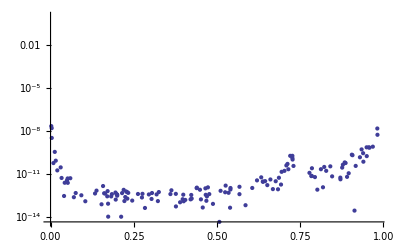

```mathematica
Module[{tP,etP,norm,fϵ,xs,exs,t1s,et1s,l,el,err},
tP={μ2-> m2,m2-> 1.,s-> 5.,q2-> -5.};
(* prepare function *)
norm={zeta2-> Zeta[2],ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z],χ-> (1-β)/(1+β),β-> Sqrt[1-ρ],ρ-> 4m2/s,χq-> (βq-1)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp-> -t1-u1,u1-> q2-s-t1};
fϵ=Coefficient[virtualRes[G]["box1"]//.norm,ϵ,{-1,0}];
(* prepare data *)
etP=(First@#->(Rationalize[Last@#/.tP,0]))&/@tP;
AppendTo[etP,sp-> s-q2];
AppendTo[etP,β-> Sqrt[1-4m2/s]];
etP=(First@#->(Last@#/.etP))&/@etP;
tP=(First@#->N@(Last@#))&/@etP;
xs=RandomReal[{0,1},150];
exs=Rationalize[#,0]&/@xs;
t1s=((-sp/2(1+β(1-2#)))/.tP)&/@xs;
et1s=((-sp/2(1+β(1-2#)))/.etP)&/@exs;
(* compute *)
l=Re@N[fϵ/.Join[tP,{t1-> t1s}]];
el=N[fϵ/.Join[etP,{t1-> et1s}],20];
err=N[Abs[(l-el)/el]];
Print@ListLogPlot[Transpose[{xs,Last@err}]];
]
```

### Vertex corrections

```mathematica
virtualRes[G]["e"]=getVirtual[G][meNLOV["e"],meNLOVDens["e"],"~/Physik/PhD/MMa/data/repE.m"];
```

```mathematica
virtualRes[G]["ecr"]=getVirtual[G][meNLOV["ecr"],meNLOVDens["ecr"],"~/Physik/PhD/MMa/data/repEcr.m"];
```

```mathematica
virtualRes[G]["g1"]=getVirtual[G][meNLOV["g1"],meNLOVDens["g1"],"~/Physik/PhD/MMa/data/repG1.m"];
```

```mathematica
virtualRes[G]["g1cr"]=getVirtual[G][meNLOV["g1cr"],meNLOVDens["g1cr"],"~/Physik/PhD/MMa/data/repG1cr.m"];
```

```mathematica
virtualRes[G]["g2"]=getVirtual[G][meNLOV["g2"],meNLOVDens["g2"],"~/Physik/PhD/MMa/data/repG2.m"];
```

```mathematica
virtualRes[G]["g2cr"]=getVirtual[G][meNLOV["g2cr"],meNLOVDens["g2cr"],"~/Physik/PhD/MMa/data/repG2cr.m"];
```

#### Commets

```mathematica
FullSimplify@Coefficient[virtualRes[G]["e"]/.{sp-> -t1-u1},ϵ,-1]
FullSimplify@Coefficient[virtualRes[G]["ecr"]/.{sp-> -t1-u1},ϵ,-1]
```

-(ⅈ (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(π^2 t1^2 u1)

-(ⅈ (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))))/(π^2 t1 u1^2)

```mathematica
FullSimplify@Coefficient[virtualRes[G]["g1"]/.{sp-> -t1-u1},ϵ,-1]
FullSimplify@Coefficient[virtualRes[G]["g1cr"]/.{sp-> -t1-u1},ϵ,-1]
```

-(ⅈ (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(π^2 t1^2 u1)

-(ⅈ (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))))/(π^2 t1 u1^2)

```mathematica
FullSimplify@Coefficient[virtualRes[G]["g2"],ϵ,-2]
FullSimplify@Coefficient[virtualRes[G]["g2cr"],ϵ,-2]
sortAndSim@Coefficient[virtualRes[G]["g2"]/.{sp-> -t1-u1},ϵ,-1]
sortAndSim@Coefficient[virtualRes[G]["g2cr"]/.{sp-> -t1-u1},ϵ,-1]
```

0

0

(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(π^2 t1^2 u1)+(ⅈ EulerGamma (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(2 π^2 t1^2 u1)-(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[4 π])/(2 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2])/(π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[m2/μ2])/(2 π^2 t1^2 u1)

-(ⅈ (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))))/(π^2 t1 u1^2)-(ⅈ EulerGamma (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))))/(2 π^2 t1 u1^2)+(ⅈ (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) ln[4 π])/(2 π^2 t1 u1^2)-(ⅈ (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) ln[-t1/m2])/(π^2 t1 u1^2)-(ⅈ (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) ln[m2/μ2])/(2 π^2 t1 u1^2)

```mathematica
sortAndSim[virtualRes[G]["g2"]/.{sp-> -t1-u1}]
```

(ⅈ EulerGamma^2 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(8 π^2 t1^2 u1)+1/(4 π^2 t1^2 u1)ⅈ EulerGamma (8 m2^2 (t1+u1)+u1 (-3 q2^2+3 q2 u1+t1 (-5 t1+u1))+m2 (3 t1^2+12 t1 u1+5 u1^2+2 q2 (3 t1+u1)))-1/(2 π^2 t1^2 u1 (m2+u1))ⅈ (-m2^2 (2 q2-t1-7 u1) (t1+u1)+u1^2 (-q2^2+q2 u1+t1 (2 t1+3 u1))+m2 u1 (q2^2-q2 (t1+u1)+2 (t1^2+5 t1 u1+u1^2)))+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) zeta2)/(8 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) Li2[(m2+u1)/m2])/(2 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[4 π]^2)/(8 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2]^2)/(2 π^2 t1^2 u1)+((ⅈ EulerGamma (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(4 π^2 t1^2 u1)+(ⅈ (8 m2^2 (t1+u1)+u1 (-3 q2^2+3 q2 u1+t1 (-5 t1+u1))+m2 (3 t1^2+12 t1 u1+5 u1^2+2 q2 (3 t1+u1))))/(4 π^2 t1^2 u1)) ln[m2/μ2]+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[m2/μ2]^2)/(8 π^2 t1^2 u1)+ln[4 π] (-(ⅈ EulerGamma (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(4 π^2 t1^2 u1)-(ⅈ (8 m2^2 (t1+u1)+u1 (-3 q2^2+3 q2 u1+t1 (-5 t1+u1))+m2 (3 t1^2+12 t1 u1+5 u1^2+2 q2 (3 t1+u1))))/(4 π^2 t1^2 u1)-(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[m2/μ2])/(4 π^2 t1^2 u1))+ln[-u1/m2] (-1/(2 π^2 t1^2 u1 (m2+u1)^2)ⅈ (16 m2^4 (t1+u1)+t1 u1^3 (q2+t1+u1)+m2^2 u1 (-3 q2^2+17 q2 t1-6 t1^2-3 q2 u1+18 t1 u1+12 u1^2)+m2^3 (6 q2 t1-3 t1^2-2 q2 u1+36 t1 u1+31 u1^2)-m2 u1^2 (5 q2^2+t1^2-2 u1^2+q2 (-11 t1+u1)))+(ⅈ EulerGamma (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(2 π^2 t1^2 u1)-(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[4 π])/(2 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[m2/μ2])/(2 π^2 t1^2 u1))+1/ϵ((ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(π^2 t1^2 u1)+(ⅈ EulerGamma (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(2 π^2 t1^2 u1)-(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[4 π])/(2 π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2])/(π^2 t1^2 u1)+(ⅈ (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[m2/μ2])/(2 π^2 t1^2 u1))

### Mass corrections

```mathematica
virtualRes[G]["m1"]=getVirtual[G][meNLOV["m1"],meNLOVDens["m1"],"~/Physik/PhD/MMa/data/repM1.m"];
```

```mathematica
virtualRes[L]["m1"]=getVirtual[L][meNLOV["m1"],meNLOVDens["m1"],"~/Physik/PhD/MMa/data/repM1.m"];
```

```mathematica
virtualRes[G]["m1cr"]=getVirtual[G][meNLOV["m1cr"],meNLOVDens["m1cr"],"~/Physik/PhD/MMa/data/repM1cr.m"];
```

```mathematica
virtualRes[L]["m1cr"]=getVirtual[L][meNLOV["m1cr"],meNLOVDens["m1cr"],"~/Physik/PhD/MMa/data/repM1cr.m"];
```

#### Comments

```mathematica
FullSimplify[BLQED/.{sp-> -t1-u1},Assumptions-> {m2>0,q2<0,u1<0,t1<0}]
Collect[sortAndSim[virtualRes[L]["m1"]/.{sp-> -t1-u1}],ϵ,FullSimplify[#,Assumptions-> {m2>0,q2<0,u1<0,t1<0}]&]
Collect[sortAndSim[virtualRes[L]["m1cr"]/.{sp-> -t1-u1}],ϵ,FullSimplify[#,Assumptions-> {m2>0,q2<0,u1<0,t1<0}]&]
```

4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)

(32 q2 (6 m2-u1) (2 m2 (t1+u1)+u1 (-q2+t1+u1)))/(t1^2 (t1+u1)^2 ϵ)-1/(t1^2 (m2+u1)^2 (t1+u1)^2)16 q2 (2 m2 (t1+u1)+u1 (-q2+t1+u1)) ((m2+u1) (8 m2^2+8 m2 u1-u1^2)+u1 (-4 m2^2-4 m2 u1+u1^2) ln[-u1/m2])

(32 q2 (6 m2-t1) (2 m2 (t1+u1)+t1 (-q2+t1+u1)))/(u1^2 (t1+u1)^2 ϵ)-(16 q2 (2 m2 (t1+u1)+t1 (-q2+t1+u1)) ((m2+t1) (8 m2^2+8 m2 t1-t1^2)+t1 (-4 m2^2-4 m2 t1+t1^2) ln[-t1/m2]))/((m2+t1)^2 u1^2 (t1+u1)^2)

### Self energy

```mathematica
Module[{l,p,line,i},
DeclareLorentzVectors[l,p];
line=Ga[ν].(Gs[l+p]+Sqrt[m2]GI).Ga[ν];
line=HEPExpand@ExplicitSlash[line];
line=line/.{
Ga[a_].GI.Ga[a_]:> Dim GI,
Ga[a_].Ga[b_].Ga[a_]:> (2-Dim)Ga[b]};
i=PaVeIntegrate[line Den[l,0] Den[l+p,Sqrt[m2]],l,muR,LoopFactor-> 1];
Print@i;
i=i/.{Div-> 0};
i=i/.{PaVe[2,muR,0][1][p2_,0,m2_]:> 1/(2p2)((m2-p2)PaVe[2,muR,0][0][p2,0,m2]-PaVe[1,muR,0][0][m2])};
i=i/.{
PaVe[1,muR,0][0][m2_]:> m2(-2/(Dim-4)+1),
PaVe[2,muR,0][0][p2_,0,m2_]:> 2/(4-Dim)+2+(m2-p2)/p2 Log[(m2-p2)/m2]
};
Print@Collect[Normal@Series[i/.{Dim-> 4+ϵ},{ϵ,0,0}],ϵ,Simplify];
]
```

(Dim GI √m2+(2-Dim) Ga[$44] p$1943[$44]) (Div+PaVe[2,muR,0][0][Sqr[p$1943],0,m2])+(2-Dim) Ga[$44] p$1943[$44] (-Div/2+PaVe[2,muR,0][1][Sqr[p$1943],0,m2])

(-8 GI √m2+2 Ga[$44] p$1943[$44])/ϵ+1/Sqr[p$1943]^2(2 GI √m2 Sqr[p$1943] (2 m2 Log[1-Sqr[p$1943]/m2]+(3-2 Log[1-Sqr[p$1943]/m2]) Sqr[p$1943])-Ga[$44] p$1943[$44] (m2+Sqr[p$1943]) (m2 Log[1-Sqr[p$1943]/m2]+Sqr[p$1943]-Log[1-Sqr[p$1943]/m2] Sqr[p$1943]))

```mathematica
Limit[(1-1/x)Log[1-x],x-> 1]
```

0

## Export

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.m",
{BGQED,BLQED,BPQED,
CoeffAG1,CoeffAL1,CoeffAP1k0,CoeffAP1k2,
CoeffAG2,CoeffAL2,CoeffAP2,
CoeffAG3,CoeffAL3,CoeffAP3,
CoeffRQED,CoeffROK,CoeffRPOKk0,CoeffRPOKk2,
SQED,SOK,EikonalFactorQED,EikonalFactorOK
}
]
```